## 1

```mathematica
Clear["Global`*"];
dim=7/2;

SpinMatrices[s_]:=Module[{d,IzMat,superDiag,Iplus,Iminus,IxMat,IyMat},(*Define the dimension of the matrices:d=2s+1*)d=2 s+1;
(*Construct Iz:a diagonal matrix with entries m=s,s-1,...,-s*)IzMat=DiagonalMatrix[Table[m,{m,s,-s,-1}]];
(*Compute the superdiagonal elements for I+*)superDiag=Table[Sqrt[s (s+1)-(s-j) (s-j+1)],{j,1,d-1}];
(*Construct I+as a dense matrix with superdiagonal elements*)Iplus=Normal[SparseArray[Band[{1,2}]->superDiag,{d,d}]];
(*Construct I-as the transpose of I+*)Iminus=Transpose[Iplus];
(*Compute Ix and Iy from I+and I-*)IxMat=(Iplus+Iminus)/2;
IyMat=(Iplus-Iminus)/(2 I);
(*Return the three spin matrices*){IxMat,IyMat,IzMat}];

(*Assign the matrices*)
{Ix3half2,Iy3half2,Iz3half2}=SpinMatrices[dim];
Hmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_]:=({{0, (√7)/2 ⅇ^(-ⅈ ϕ1), 0, 0, 0, 0, 0, 0}, {(√7)/2 ⅇ^(ⅈ ϕ1), 0, √3 ⅇ^(-ⅈ ϕ2), 0, 0, 0, 0, 0}, {0, √3 ⅇ^(ⅈ ϕ2), 0, (√15)/2 ⅇ^(-ⅈ ϕ3), 0, 0, 0, 0}, {0, 0, (√15)/2 ⅇ^(ⅈ ϕ3), 0, 2 ⅇ^(-ⅈ ϕ4), 0, 0, 0}, {0, 0, 0, 2 ⅇ^(ⅈ ϕ4), 0, (√15)/2 ⅇ^(-ⅈ ϕ5), 0, 0}, {0, 0, 0, 0, (√15)/2 ⅇ^(ⅈ ϕ5), 0, √3 ⅇ^(-ⅈ ϕ6), 0}, {0, 0, 0, 0, 0, √3 ⅇ^(ⅈ ϕ6), 0, (√7)/2 ⅇ^(-ⅈ ϕ7)}, {0, 0, 0, 0, 0, 0, (√7)/2 ⅇ^(ⅈ ϕ7), 0}});
Iplus5half2=Ix3half2+I*Iy3half2;
Iminus5half2=Ix3half2-I*Iy3half2;
UHmuti[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_]:=MatrixExp[-I*Hmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7]*t] 
IniPhi={{1},{0},{0},{0},{0},{0},{0},{0}};

(*StateθϕInitial[θ_,ϕ_]:=MatrixExp[I*θ(Sin[ϕ]*Ix3half2-Cos[ϕ]*Iy3half2)].IniPhi*)

StateθϕInitial[θ_,ϕ_]:={{Cos[θ/2]^7},{√7 ⅇ^(ⅈ ϕ) Cos[θ/2]^6 Sin[θ/2]},{√21 ⅇ^(2 ⅈ ϕ) Cos[θ/2]^5 Sin[θ/2]^2},{1/16 √35 ⅇ^(3 ⅈ ϕ) Csc[θ/2] Sin[θ]^4},{1/8 √35 ⅇ^(4 ⅈ ϕ) Sin[θ/2] Sin[θ]^3},{1/4 √21 ⅇ^(5 ⅈ ϕ) Sin[θ/2]^3 Sin[θ]^2},{1/2 √7 ⅇ^(6 ⅈ ϕ) Sin[θ/2]^5 Sin[θ]},{ⅇ^(7 ⅈ ϕ) Sin[θ/2]^7}}

StateEvo[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,θ_,ϕ_]:=UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].StateθϕInitial[θ,ϕ]
θ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
Chop[N[First[Flatten[ArcCos[zVal/Sqrt[xVal^2+yVal^2+zVal^2]]]]]]
]
ϕ1[state1_]:=Module[{st=state1},
xVal=ConjugateTranspose[st].Ix3half2.st;
yVal=ConjugateTranspose[st].Iy3half2.st;
zVal=ConjugateTranspose[st].Iz3half2.st;
If[Chop[N[First[Flatten[yVal]]]]>0,N[First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]],Chop[N[2Pi-First[Flatten[ArcCos[xVal/(Sqrt[xVal^2+yVal^2+zVal^2]Sin[θ1[st]])]]]]]]
]

In1[state_]:=Chop[N[-Ix3half2*Sin[ϕ1[state]]+Iy3half2*Cos[ϕ1[state]]]]
In2[state_]:=Chop[N[-Ix3half2*Cos[θ1[state]]Cos[ϕ1[state]]-Iy3half2*Cos[θ1[state]]Sin[ϕ1[state]]+Iz3half2*Sin[θ1[state]]]]
In1n2plusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]+In2[state].In2[state]).state]]
In1n2minusSqure[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In1[state]-In2[state].In2[state]).state]]
In1n2n2n1[state_]:=Chop[N[ConjugateTranspose[state].(In1[state].In2[state]+In2[state].In1[state]).state]]
ξSqure[state_]:=Chop[N[First[Flatten[ (In1n2plusSqure[state]-√((In1n2minusSqure[state])^2+(In1n2n2n1[state])^2) )]]],10^-8]
```

```mathematica
StateEvo[ϕ11,ϕ2,ϕ3,Pi/2,Pi-ϕ3,Pi-ϕ2,Pi-ϕ11,t,Pi/2,Pi/2]//FullSimplify
```

```mathematica
st7half2={{(ⅇ^(-1/2 ⅈ (7 t+2 (ϕ11+ϕ2+ϕ3))) (-7 ⅈ ⅇ^(ⅈ (ϕ2+ϕ3)) (-1-9 ⅇ^(2 ⅈ t)+5 ⅇ^(4 ⅈ t)+5 ⅇ^(6 ⅈ t))+7 (-1+ⅇ^(2 ⅈ t))^2 (5 ⅈ (-1+ⅇ^(2 ⅈ t))-3 ⅇ^(ⅈ ϕ3) (1+3 ⅇ^(2 ⅈ t)))+ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (1+7 ⅇ^(2 ⅈ t) (3+5 ⅇ^(2 ⅈ t)+ⅇ^(4 ⅈ t)))))/(512 √2)},{1/512 √(7/2) ⅇ^(-1/2 ⅈ (7 t+2 (ϕ2+ϕ3))) (-35 ⅈ+45 ⅈ ⅇ^(2 ⅈ t)+15 ⅈ ⅇ^(4 ⅈ t)-25 ⅈ ⅇ^(6 ⅈ t)-21 ⅇ^(ⅈ ϕ3)-9 ⅇ^(ⅈ (2 t+ϕ3))-15 ⅇ^(ⅈ (4 t+ϕ3))+45 ⅇ^(ⅈ (6 t+ϕ3))+7 ⅈ ⅇ^(ⅈ (ϕ2+ϕ3))+27 ⅈ ⅇ^(ⅈ (2 t+ϕ2+ϕ3))+5 ⅈ ⅇ^(ⅈ (4 t+ϕ2+ϕ3))+25 ⅈ ⅇ^(ⅈ (6 t+ϕ2+ϕ3))+ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (1+9 ⅇ^(2 ⅈ t)-5 ⅇ^(4 ⅈ t)-5 ⅇ^(6 ⅈ t)))},{1/512 √(21/2) ⅇ^(-1/2 ⅈ (7 t+2 ϕ3)) (-35 ⅈ+ⅇ^(ⅈ ϕ3) (-21+ⅇ^(ⅈ ϕ2) (7 ⅈ+ⅇ^(ⅈ ϕ11)))+ⅇ^(2 ⅈ t) (5 ⅈ+ⅇ^(ⅈ ϕ3) (-1+ⅇ^(ⅈ ϕ2) (3 ⅈ+ⅇ^(ⅈ ϕ11))))+3 ⅇ^(6 ⅈ t) (5 ⅈ+ⅇ^(ⅈ ϕ3) (-9+ⅇ^(ⅈ ϕ2) (-5 ⅈ+ⅇ^(ⅈ ϕ11))))-5 ⅇ^(4 ⅈ t) (-3 ⅈ+ⅇ^(ⅈ ϕ3) (3-ⅈ Cos[ϕ2]+Cos[ϕ11+ϕ2]+Sin[ϕ2]+ⅈ Sin[ϕ11+ϕ2])))},{-1/512 √(35/2) ⅇ^(-(7 ⅈ t)/2) (35 ⅈ+15 ⅈ ⅇ^(2 ⅈ t)+9 ⅈ ⅇ^(4 ⅈ t)+5 ⅈ ⅇ^(6 ⅈ t)+21 ⅇ^(ⅈ ϕ3)-3 ⅇ^(ⅈ (2 t+ϕ3))-9 ⅇ^(ⅈ (4 t+ϕ3))-9 ⅇ^(ⅈ (6 t+ϕ3))-7 ⅈ ⅇ^(ⅈ (ϕ2+ϕ3))+9 ⅈ ⅇ^(ⅈ (2 t+ϕ2+ϕ3))+3 ⅈ ⅇ^(ⅈ (4 t+ϕ2+ϕ3))-5 ⅈ ⅇ^(ⅈ (6 t+ϕ2+ϕ3))+ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(2 ⅈ t))^3)},{1/512 √(35/2) ⅇ^(-(7 ⅈ t)/2) (35+15 ⅇ^(2 ⅈ t)+9 ⅇ^(4 ⅈ t)+5 ⅇ^(6 ⅈ t)-21 ⅈ ⅇ^(ⅈ ϕ3)+3 ⅈ ⅇ^(ⅈ (2 t+ϕ3))+9 ⅈ ⅇ^(ⅈ (4 t+ϕ3))+9 ⅈ ⅇ^(ⅈ (6 t+ϕ3))-7 ⅇ^(ⅈ (ϕ2+ϕ3))+9 ⅇ^(ⅈ (2 t+ϕ2+ϕ3))+3 ⅇ^(ⅈ (4 t+ϕ2+ϕ3))-5 ⅇ^(ⅈ (6 t+ϕ2+ϕ3))-ⅈ ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(2 ⅈ t))^3)},{1/512 √(21/2) ⅇ^(-1/2 ⅈ (7 t+2 ϕ3)) (-35+5 ⅇ^(2 ⅈ t)+15 ⅇ^(4 ⅈ t)+15 ⅇ^(6 ⅈ t)+21 ⅈ ⅇ^(ⅈ ϕ3)+ⅈ ⅇ^(ⅈ (2 t+ϕ3))+15 ⅈ ⅇ^(ⅈ (4 t+ϕ3))+27 ⅈ ⅇ^(ⅈ (6 t+ϕ3))+7 ⅇ^(ⅈ (ϕ2+ϕ3))+3 ⅇ^(ⅈ (2 t+ϕ2+ϕ3))+5 ⅇ^(ⅈ (4 t+ϕ2+ϕ3))-15 ⅇ^(ⅈ (6 t+ϕ2+ϕ3))-ⅈ ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(2 ⅈ t))^2 (1+3 ⅇ^(2 ⅈ t)))},{1/512 √(7/2) ⅇ^(-1/2 ⅈ (7 t+2 (ϕ2+ϕ3))) (35-45 ⅇ^(2 ⅈ t)-15 ⅇ^(4 ⅈ t)+25 ⅇ^(6 ⅈ t)-21 ⅈ ⅇ^(ⅈ ϕ3)-9 ⅈ ⅇ^(ⅈ (2 t+ϕ3))-15 ⅈ ⅇ^(ⅈ (4 t+ϕ3))+45 ⅈ ⅇ^(ⅈ (6 t+ϕ3))-7 ⅇ^(ⅈ (ϕ2+ϕ3))-27 ⅇ^(ⅈ (2 t+ϕ2+ϕ3))-5 ⅇ^(ⅈ (4 t+ϕ2+ϕ3))-25 ⅇ^(ⅈ (6 t+ϕ2+ϕ3))-ⅈ ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (-1-9 ⅇ^(2 ⅈ t)+5 ⅇ^(4 ⅈ t)+5 ⅇ^(6 ⅈ t)))},{(ⅇ^(-1/2 ⅈ (7 t+2 (ϕ11+ϕ2+ϕ3))) (-7 ⅇ^(ⅈ (ϕ2+ϕ3)) (-1-9 ⅇ^(2 ⅈ t)+5 ⅇ^(4 ⅈ t)+5 ⅇ^(6 ⅈ t))+7 (-1+ⅇ^(2 ⅈ t))^2 (-5+5 ⅇ^(2 ⅈ t)+3 ⅈ ⅇ^(ⅈ ϕ3) (1+3 ⅇ^(2 ⅈ t)))-ⅈ ⅇ^(ⅈ (ϕ11+ϕ2+ϕ3)) (1+7 ⅇ^(2 ⅈ t) (3+5 ⅇ^(2 ⅈ t)+ⅇ^(4 ⅈ t)))))/(512 √2)}};
```

```mathematica
ConjugateTranspose[st7half2]
```

```mathematica
ConTranst7half2={{(ⅇ^(1/2 ⅈ (7 t+2 (ϕ11+ϕ2+ϕ3))) (-7 (-ⅈ) ⅇ^((-ⅈ) (ϕ2+ϕ3)) (-1-9 ⅇ^(2 (-ⅈ) t)+5 ⅇ^(4 (-ⅈ) t)+5 ⅇ^(6 (-ⅈ) t))+7 (-1+ⅇ^(2 (-ⅈ) t))^2 (5 (-ⅈ) (-1+ⅇ^(2 (-ⅈ) t))-3 ⅇ^((-ⅈ) ϕ3) (1+3 ⅇ^(2 (-ⅈ) t)))+ⅇ^((-ⅈ) (ϕ11+ϕ2+ϕ3)) (1+7 ⅇ^(2 (-ⅈ) t) (3+5 ⅇ^(2 (-ⅈ) t)+ⅇ^(4 (-ⅈ) t)))))/(512 √2),1/512 √(7/2) ⅇ^(1/2 ⅈ (7 t+2 (ϕ2+ϕ3))) (35 ⅈ-45 ⅈ ⅇ^(-2 ⅈ t)-15 ⅈ ⅇ^(-4 ⅈ t)+25 ⅈ ⅇ^(-6 ⅈ t)-21 ⅇ^(-ⅈ ϕ3)-7 ⅈ ⅇ^(-ⅈ (ϕ2+ϕ3))+(-9 ⅇ^((-ⅈ) (2 t+ϕ3))-15 ⅇ^((-ⅈ) (4 t+ϕ3))+45 ⅇ^((-ⅈ) (6 t+ϕ3))+27 (-ⅈ) ⅇ^((-ⅈ) (2 t+ϕ2+ϕ3))+5 (-ⅈ) ⅇ^((-ⅈ) (4 t+ϕ2+ϕ3))+25 (-ⅈ) ⅇ^((-ⅈ) (6 t+ϕ2+ϕ3))+ⅇ^((-ⅈ) (ϕ11+ϕ2+ϕ3)) (1+9 ⅇ^(2 (-ⅈ) t)-5 ⅇ^(4 (-ⅈ) t)-5 ⅇ^(6 (-ⅈ) t)))),1/512 √(21/2) ⅇ^(1/2 ⅈ (7 t+2 ϕ3)) (35 ⅈ+(ⅇ^((-ⅈ) ϕ3) (-21+ⅇ^((-ⅈ) ϕ2) (7 (-ⅈ)+ⅇ^((-ⅈ) ϕ11)))+ⅇ^(2 (-ⅈ) t) (5 (-ⅈ)+ⅇ^((-ⅈ) ϕ3) (-1+ⅇ^((-ⅈ) ϕ2) (3 (-ⅈ)+ⅇ^((-ⅈ) ϕ11))))+3 ⅇ^(6 (-ⅈ) t) (5 (-ⅈ)+ⅇ^((-ⅈ) ϕ3) (-9+ⅇ^((-ⅈ) ϕ2) (-5 (-ⅈ)+ⅇ^((-ⅈ) ϕ11))))-5 ⅇ^(4 (-ⅈ) t) (-3 (-ⅈ)+ⅇ^((-ⅈ) ϕ3) (3-(-ⅈ) Cos[ϕ2]+Cos[ϕ11+ϕ2]+Sin[ϕ2]+(-ⅈ) Sin[ϕ11+ϕ2])))),-1/512 √(35/2) ⅇ^(7/2 ⅈ t) (-35 ⅈ-15 ⅈ ⅇ^(-2 ⅈ t)-9 ⅈ ⅇ^(-4 ⅈ t)-5 ⅈ ⅇ^(-6 ⅈ t)+21 ⅇ^(-ⅈ ϕ3)+7 ⅈ ⅇ^(-ⅈ (ϕ2+ϕ3))+(-3 ⅇ^((-ⅈ) (2 t+ϕ3))-9 ⅇ^((-ⅈ) (4 t+ϕ3))-9 ⅇ^((-ⅈ) (6 t+ϕ3))+9 (-ⅈ) ⅇ^((-ⅈ) (2 t+ϕ2+ϕ3))+3 (-ⅈ) ⅇ^((-ⅈ) (4 t+ϕ2+ϕ3))-5 (-ⅈ) ⅇ^((-ⅈ) (6 t+ϕ2+ϕ3))+ⅇ^((-ⅈ) (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(2 (-ⅈ) t))^3)),1/512 √(35/2) ⅇ^(7/2 ⅈ t) (35+15 ⅇ^(-2 ⅈ t)+9 ⅇ^(-4 ⅈ t)+5 ⅇ^(-6 ⅈ t)+21 ⅈ ⅇ^(-ⅈ ϕ3)-7 ⅇ^(-ⅈ (ϕ2+ϕ3))+(3 (-ⅈ) ⅇ^((-ⅈ) (2 t+ϕ3))+9 (-ⅈ) ⅇ^((-ⅈ) (4 t+ϕ3))+9 (-ⅈ) ⅇ^((-ⅈ) (6 t+ϕ3))+9 ⅇ^((-ⅈ) (2 t+ϕ2+ϕ3))+3 ⅇ^((-ⅈ) (4 t+ϕ2+ϕ3))-5 ⅇ^((-ⅈ) (6 t+ϕ2+ϕ3))-(-ⅈ) ⅇ^((-ⅈ) (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(2 (-ⅈ) t))^3)),1/512 √(21/2) ⅇ^(1/2 ⅈ (7 t+2 ϕ3)) (-35+5 ⅇ^(-2 ⅈ t)+15 ⅇ^(-4 ⅈ t)+15 ⅇ^(-6 ⅈ t)-21 ⅈ ⅇ^(-ⅈ ϕ3)+7 ⅇ^(-ⅈ (ϕ2+ϕ3))+((-ⅈ) ⅇ^((-ⅈ) (2 t+ϕ3))+15 (-ⅈ) ⅇ^((-ⅈ) (4 t+ϕ3))+27 (-ⅈ) ⅇ^((-ⅈ) (6 t+ϕ3))+3 ⅇ^((-ⅈ) (2 t+ϕ2+ϕ3))+5 ⅇ^((-ⅈ) (4 t+ϕ2+ϕ3))-15 ⅇ^((-ⅈ) (6 t+ϕ2+ϕ3))-(-ⅈ) ⅇ^((-ⅈ) (ϕ11+ϕ2+ϕ3)) (-1+ⅇ^(2 (-ⅈ) t))^2 (1+3 ⅇ^(2 (-ⅈ) t)))),1/512 √(7/2) ⅇ^(1/2 ⅈ (7 t+2 (ϕ2+ϕ3))) (35-45 ⅇ^(-2 ⅈ t)-15 ⅇ^(-4 ⅈ t)+25 ⅇ^(-6 ⅈ t)+21 ⅈ ⅇ^(-ⅈ ϕ3)-7 ⅇ^(-ⅈ (ϕ2+ϕ3))+(-9 (-ⅈ) ⅇ^((-ⅈ) (2 t+ϕ3))-15 (-ⅈ) ⅇ^((-ⅈ) (4 t+ϕ3))+45 (-ⅈ) ⅇ^((-ⅈ) (6 t+ϕ3))-27 ⅇ^((-ⅈ) (2 t+ϕ2+ϕ3))-5 ⅇ^((-ⅈ) (4 t+ϕ2+ϕ3))-25 ⅇ^((-ⅈ) (6 t+ϕ2+ϕ3))-(-ⅈ) ⅇ^((-ⅈ) (ϕ11+ϕ2+ϕ3)) (-1-9 ⅇ^(2 (-ⅈ) t)+5 ⅇ^(4 (-ⅈ) t)+5 ⅇ^(6 (-ⅈ) t)))),(ⅇ^(1/2 ⅈ (7 t+2 (ϕ11+ϕ2+ϕ3))) (-7 ⅇ^((-ⅈ) (ϕ2+ϕ3)) (-1-9 ⅇ^(2 (-ⅈ) t)+5 ⅇ^(4 (-ⅈ) t)+5 ⅇ^(6 (-ⅈ) t))+7 (-1+ⅇ^(2 (-ⅈ) t))^2 (-5+5 ⅇ^(2 (-ⅈ) t)+3 (-ⅈ) ⅇ^((-ⅈ) ϕ3) (1+3 ⅇ^(2 (-ⅈ) t)))-(-ⅈ) ⅇ^((-ⅈ) (ϕ11+ϕ2+ϕ3)) (1+7 ⅇ^(2 (-ⅈ) t) (3+5 ⅇ^(2 (-ⅈ) t)+ⅇ^(4 (-ⅈ) t)))))/(512 √2)}};
```

```mathematica
ConTranst7half2.Ix3half2.st7half2//FullSimplify
```

{{0}}

```mathematica
ConTranst7half2.Iy3half2.st7half2//FullSimplify
```

ConTranst7half2.Iy3half2.st7half2

```mathematica
ConTranst7half2.Iz3half2.st7half2//FullSimplify
```

{{0}}

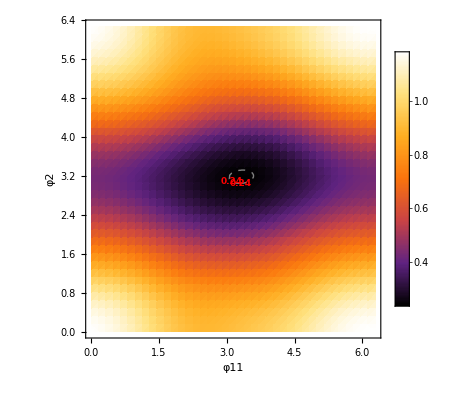

```mathematica
φ3=2.9;
AA1=Show[(*主密度图-保持完整显示*)DensityPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,φ3,Pi/2,Pi-φ3,Pi-φ2,Pi-φ11,0.314,Pi/2,Pi/2]]]]/(7/2),{φ11,0,2Pi},{φ2,0,2Pi},PlotLegends->Automatic,ColorFunction->"SunsetColors",PlotPoints->40,FrameLabel->{"φ11","φ2"},LabelStyle->{Bold,12}],(*青色区域:仅填充<0.25 区域，不遮挡其他部分*)ContourPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,φ3,Pi/2,Pi-φ3,Pi-φ2,Pi-φ11,0.314,Pi/2,Pi/2]]]]/(7/2),{φ11,0,2Pi},{φ2,0,2Pi},Contours->Range[0.15,0.24,0.005],(*仅<0.5 的等高线值*)ContourLabels->(Text[Style[#3,9,Bold,Red],{#1,#2}]&),(*红色标签*)ContourStyle->Directive[Gray,Thick,Dashed],(*黑色虚线*)PlotPoints->40,ContourShading->None  (*🔥 关键修复:禁用背景填充!*)]]
```

```mathematica
Export["D:\\desksave2\\Astro\\spin squeezing\\picture save\\φ11φ2 φ3 2p9 7half2.pdf",AA1]
```

D:\desksave2\Astro\spin squeezing\picture save\φ11φ2 φ3 2p9 7half2.pdf

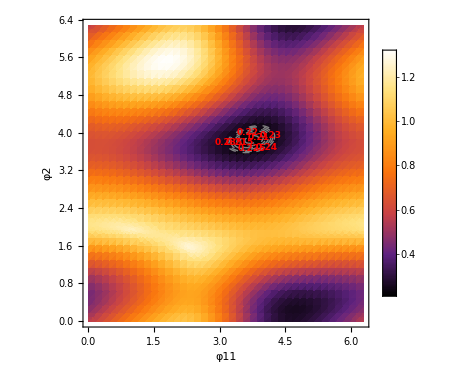

```mathematica
φ3=1;
AA1=Show[(*主密度图-保持完整显示*)DensityPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,φ3,Pi/2,Pi-φ3,Pi-φ2,Pi-φ11,0.314,Pi/2,Pi/2]]]]/(7/2),{φ11,0,2Pi},{φ2,0,2Pi},PlotLegends->Automatic,ColorFunction->"SunsetColors",PlotPoints->40,FrameLabel->{"φ11","φ2"},LabelStyle->{Bold,12}],(*青色区域:仅填充<0.25 区域，不遮挡其他部分*)ContourPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,φ3,Pi/2,Pi-φ3,Pi-φ2,Pi-φ11,0.314,Pi/2,Pi/2]]]]/(7/2),{φ11,0,2Pi},{φ2,0,2Pi},Contours->Range[0.15,0.24,0.005],(*仅<0.5 的等高线值*)ContourLabels->(Text[Style[#3,9,Bold,Red],{#1,#2}]&),(*红色标签*)ContourStyle->Directive[Gray,Thick,Dashed],(*黑色虚线*)PlotPoints->40,ContourShading->None  (*🔥 关键修复:禁用背景填充!*)]]
```

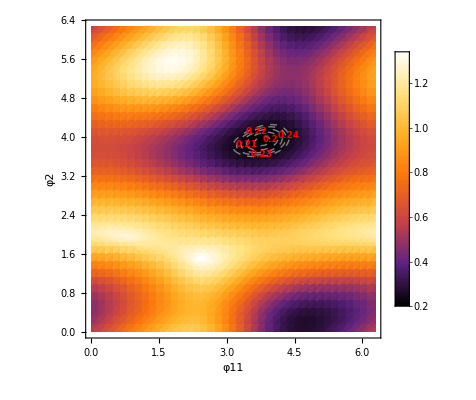

```mathematica
φ3=0.9;
AA2=Show[(*主密度图-保持完整显示*)DensityPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,φ3,Pi/2,Pi-φ3,Pi-φ2,Pi-φ11,0.314,Pi/2,Pi/2]]]]/(7/2),{φ11,0,2Pi},{φ2,0,2Pi},PlotLegends->Automatic,ColorFunction->"SunsetColors",PlotPoints->40,FrameLabel->{"φ11","φ2"},LabelStyle->{Bold,12}],(*青色区域:仅填充<0.25 区域，不遮挡其他部分*)ContourPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,φ3,Pi/2,Pi-φ3,Pi-φ2,Pi-φ11,0.314,Pi/2,Pi/2]]]]/(7/2),{φ11,0,2Pi},{φ2,0,2Pi},Contours->Range[0.15,0.24,0.01],(*仅<0.5 的等高线值*)ContourLabels->(Text[Style[#3,9,Bold,Red],{#1,#2}]&),(*红色标签*)ContourStyle->Directive[Gray,Thick,Dashed],(*黑色虚线*)PlotPoints->40,ContourShading->None  (*🔥 关键修复:禁用背景填充!*)]]
```

```mathematica
Export["D:\\desksave2\\Astro\\spin squeezing\\picture save\\φ11φ2 φ3 0p9 7half2.pdf",AA2]
```

D:\desksave2\Astro\spin squeezing\picture save\φ11φ2 φ3 0p9 7half2.pdf

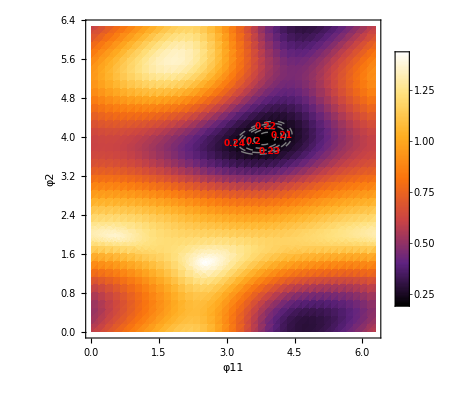

```mathematica
φ3=0.8;
AA3=Show[(*主密度图-保持完整显示*)DensityPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,φ3,Pi/2,Pi-φ3,Pi-φ2,Pi-φ11,0.314,Pi/2,Pi/2]]]]/(7/2),{φ11,0,2Pi},{φ2,0,2Pi},PlotLegends->Automatic,ColorFunction->"SunsetColors",PlotPoints->40,FrameLabel->{"φ11","φ2"},LabelStyle->{Bold,12}],(*青色区域:仅填充<0.25 区域，不遮挡其他部分*)ContourPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,φ3,Pi/2,Pi-φ3,Pi-φ2,Pi-φ11,0.314,Pi/2,Pi/2]]]]/(7/2),{φ11,0,2Pi},{φ2,0,2Pi},Contours->Range[0.15,0.24,0.01],(*仅<0.5 的等高线值*)ContourLabels->(Text[Style[#3,9,Bold,Red],{#1,#2}]&),(*红色标签*)ContourStyle->Directive[Gray,Thick,Dashed],(*黑色虚线*)PlotPoints->40,ContourShading->None  (*🔥 关键修复:禁用背景填充!*)]]
```

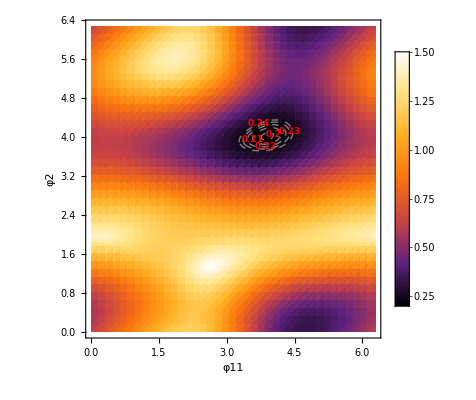

```mathematica
φ3=0.7;
AA4=Show[(*主密度图-保持完整显示*)DensityPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,φ3,Pi/2,Pi-φ3,Pi-φ2,Pi-φ11,0.314,Pi/2,Pi/2]]]]/(7/2),{φ11,0,2Pi},{φ2,0,2Pi},PlotLegends->Automatic,ColorFunction->"SunsetColors",PlotPoints->40,FrameLabel->{"φ11","φ2"},LabelStyle->{Bold,12}],(*青色区域:仅填充<0.25 区域，不遮挡其他部分*)ContourPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,φ3,Pi/2,Pi-φ3,Pi-φ2,Pi-φ11,0.314,Pi/2,Pi/2]]]]/(7/2),{φ11,0,2Pi},{φ2,0,2Pi},Contours->Range[0.15,0.24,0.01],(*仅<0.5 的等高线值*)ContourLabels->(Text[Style[#3,9,Bold,Red],{#1,#2}]&),(*红色标签*)ContourStyle->Directive[Gray,Thick,Dashed],(*黑色虚线*)PlotPoints->40,ContourShading->None  (*🔥 关键修复:禁用背景填充!*)]]
```

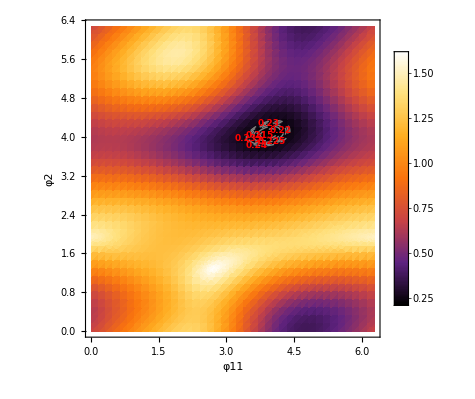

```mathematica
φ3=0.6;
AA6=Show[(*主密度图-保持完整显示*)DensityPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,φ3,Pi/2,Pi-φ3,Pi-φ2,Pi-φ11,0.314,Pi/2,Pi/2]]]]/(7/2),{φ11,0,2Pi},{φ2,0,2Pi},PlotLegends->Automatic,ColorFunction->"SunsetColors",PlotPoints->40,FrameLabel->{"φ11","φ2"},LabelStyle->{Bold,12}],(*青色区域:仅填充<0.25 区域，不遮挡其他部分*)ContourPlot[ξSqure[Chop[N[StateEvo[φ11,φ2,φ3,Pi/2,Pi-φ3,Pi-φ2,Pi-φ11,0.314,Pi/2,Pi/2]]]]/(7/2),{φ11,0,2Pi},{φ2,0,2Pi},Contours->Range[0.15,0.24,0.005],(*仅<0.5 的等高线值*)ContourLabels->(Text[Style[#3,9,Bold,Red],{#1,#2}]&),(*红色标签*)ContourStyle->Directive[Gray,Thick,Dashed],(*黑色虚线*)PlotPoints->40,ContourShading->None  (*🔥 关键修复:禁用背景填充!*)]]
```

```mathematica
phi2=Pi/2;

ϕ1gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,phi1_,phi2_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1-10^-8,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]])
ϕ2gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,phi1_,phi2_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2-10^-8,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]])
ϕ3gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,phi1_,phi2_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3-10^-8,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]])
ϕ4gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,phi1_,phi2_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4-10^-8,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]])
ϕ5gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,phi1_,phi2_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5-10^-8,ϕ6,ϕ7,t,phi1,phi2]]]])
ϕ6gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,phi1_,phi2_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6-10^-8,ϕ7,t,phi1,phi2]]]])
ϕ7gra[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,phi1_,phi2_]:=1/10^-8(ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t,phi1,phi2]]]]-ξSqure[Chop[N[StateEvo[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7-10^-8,t,phi1,phi2]]]])

ϕ1graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1-10^-8,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]])/10^-8
ϕ2graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2-10^-8,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]])/10^-8
ϕ3graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3-10^-8,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]])/10^-8
ϕ4graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:=(ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4-10^-8,ϕ5,ϕ6,ϕ7,t].state]]])/10^-8
ϕ5graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:= (ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5-10^-8,ϕ6,ϕ7,t].state]]])/10^-8
ϕ6graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:= (ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6-10^-8,ϕ7,t].state]]])/10^-8
ϕ7graState[ϕ1_,ϕ2_,ϕ3_,ϕ4_,ϕ5_,ϕ6_,ϕ7_,t_,state_]:= (ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,t].state]]]-ξSqure[Chop[N[UHmuti[ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7-10^-8,t].state]]])/10^-8
```

False

```mathematica
durationnumber=1;
avenumber=500;
SqueezeTableduration=Table[Table[0,{i,1,avenumber}],{i,1,durationnumber+1}];
SqueezeTableduration2=Table[Table[0,{i,1,avenumber}],{i,1,durationnumber+1}];
phiMinTableduration=Table[Table[0,{i,1,avenumber}],{i,1,durationnumber+1}];
Do[
Do[
If[Divisible[k,1],Print["durationnumber:",k,"  avenumber:",m]];
totT=0.314;
phi1=Pi/2;
itenumber=250;
ϕTable=Table[{RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi],RandomReal[Pi]},{i,1,itenumber}];

SqueezeTable=Table[0,{i,1,itenumber}];

SqueezeTable[[1]]=ξSqure[Chop[N[StateEvo[ϕTable[[1,1]],ϕTable[[1,2]],ϕTable[[1,3]],ϕTable[[1,4]],ϕTable[[1,5]],ϕTable[[1,6]],ϕTable[[1,7]],totT,phi1,phi2]]]];
Do[ 
ϕTable[[i,1]]=ϕTable[[i-1,1]]-0.4*ϕ1gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT,phi1,phi2];
ϕTable[[i,2]]=ϕTable[[i-1,2]]-0.4*ϕ2gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT,phi1,phi2];
ϕTable[[i,3]]=ϕTable[[i-1,3]]-0.4*ϕ3gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT,phi1,phi2];
ϕTable[[i,4]]=ϕTable[[i-1,4]]-0.4*ϕ4gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT,phi1,phi2];
ϕTable[[i,5]]=ϕTable[[i-1,5]]-0.4*ϕ5gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT,phi1,phi2];
ϕTable[[i,6]]=ϕTable[[i-1,6]]-0.4*ϕ6gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT,phi1,phi2];
ϕTable[[i,7]]=ϕTable[[i-1,7]]-0.4*ϕ7gra[ϕTable[[i-1,1]],ϕTable[[i-1,2]],ϕTable[[i-1,3]],ϕTable[[i-1,4]],ϕTable[[i-1,5]],ϕTable[[i-1,6]],ϕTable[[i-1,7]],totT,phi1,phi2];
SqueezeTable[[i]]=ξSqure[Chop[N[StateEvo[ϕTable[[i,1]],ϕTable[[i,2]],ϕTable[[i,3]],ϕTable[[i,4]],ϕTable[[i,5]],ϕTable[[i,6]],ϕTable[[i,7]],totT,phi1,phi2]]]];

If[Divisible[i,100],Print[N[i/itenumber]," avenumber ",N[m/avenumber]]];
,{i,2,itenumber}];

SqueezeTableduration[[k,m]]=Min[SqueezeTable];
phiMinTableduration[[k,m]]=ϕTable[[Flatten[Position[SqueezeTable,Min[SqueezeTable]]][[1]]]];

SqueezeTableduration[[k,m]]=Min[SqueezeTable];



,{k,1,durationnumber+1}]
,{m,1,avenumber}]
```

durationnumber:1  avenumber:1

0.4 avenumber 0.002

0.8 avenumber 0.002

durationnumber:2  avenumber:1

0.4 avenumber 0.002

0.8 avenumber 0.002

durationnumber:1  avenumber:2

0.4 avenumber 0.004

0.8 avenumber 0.004

durationnumber:2  avenumber:2

0.4 avenumber 0.004

0.8 avenumber 0.004

durationnumber:1  avenumber:3

0.4 avenumber 0.006

0.8 avenumber 0.006

durationnumber:2  avenumber:3

0.4 avenumber 0.006

0.8 avenumber 0.006

durationnumber:1  avenumber:4

0.4 avenumber 0.008

0.8 avenumber 0.008

durationnumber:2  avenumber:4

0.4 avenumber 0.008

0.8 avenumber 0.008

durationnumber:1  avenumber:5

0.4 avenumber 0.01

0.8 avenumber 0.01

durationnumber:2  avenumber:5

0.4 avenumber 0.01

0.8 avenumber 0.01

durationnumber:1  avenumber:6

0.4 avenumber 0.012

0.8 avenumber 0.012

durationnumber:2  avenumber:6

0.4 avenumber 0.012

0.8 avenumber 0.012

durationnumber:1  avenumber:7

0.4 avenumber 0.014

0.8 avenumber 0.014

durationnumber:2  avenumber:7

0.4 avenumber 0.014

0.8 avenumber 0.014

durationnumber:1  avenumber:8

0.4 avenumber 0.016

0.8 avenumber 0.016

durationnumber:2  avenumber:8

0.4 avenumber 0.016

0.8 avenumber 0.016

durationnumber:1  avenumber:9

0.4 avenumber 0.018

0.8 avenumber 0.018

durationnumber:2  avenumber:9

0.4 avenumber 0.018

0.8 avenumber 0.018

durationnumber:1  avenumber:10

0.4 avenumber 0.02

0.8 avenumber 0.02

durationnumber:2  avenumber:10

0.4 avenumber 0.02

0.8 avenumber 0.02

durationnumber:1  avenumber:11

0.4 avenumber 0.022

0.8 avenumber 0.022

durationnumber:2  avenumber:11

0.4 avenumber 0.022

0.8 avenumber 0.022

durationnumber:1  avenumber:12

0.4 avenumber 0.024

0.8 avenumber 0.024

durationnumber:2  avenumber:12

0.4 avenumber 0.024

0.8 avenumber 0.024

durationnumber:1  avenumber:13

0.4 avenumber 0.026

0.8 avenumber 0.026

durationnumber:2  avenumber:13

0.4 avenumber 0.026

0.8 avenumber 0.026

durationnumber:1  avenumber:14

0.4 avenumber 0.028

0.8 avenumber 0.028

durationnumber:2  avenumber:14

0.4 avenumber 0.028

0.8 avenumber 0.028

durationnumber:1  avenumber:15

0.4 avenumber 0.03

0.8 avenumber 0.03

durationnumber:2  avenumber:15

0.4 avenumber 0.03

0.8 avenumber 0.03

durationnumber:1  avenumber:16

0.4 avenumber 0.032

0.8 avenumber 0.032

durationnumber:2  avenumber:16

0.4 avenumber 0.032

0.8 avenumber 0.032

durationnumber:1  avenumber:17

0.4 avenumber 0.034

0.8 avenumber 0.034

durationnumber:2  avenumber:17

0.4 avenumber 0.034

0.8 avenumber 0.034

durationnumber:1  avenumber:18

0.4 avenumber 0.036

0.8 avenumber 0.036

durationnumber:2  avenumber:18

0.4 avenumber 0.036

0.8 avenumber 0.036

durationnumber:1  avenumber:19

0.4 avenumber 0.038

0.8 avenumber 0.038

durationnumber:2  avenumber:19

0.4 avenumber 0.038

0.8 avenumber 0.038

durationnumber:1  avenumber:20

0.4 avenumber 0.04

0.8 avenumber 0.04

durationnumber:2  avenumber:20

0.4 avenumber 0.04

0.8 avenumber 0.04

durationnumber:1  avenumber:21

0.4 avenumber 0.042

0.8 avenumber 0.042

durationnumber:2  avenumber:21

0.4 avenumber 0.042

0.8 avenumber 0.042

durationnumber:1  avenumber:22

0.4 avenumber 0.044

0.8 avenumber 0.044

durationnumber:2  avenumber:22

0.4 avenumber 0.044

0.8 avenumber 0.044

durationnumber:1  avenumber:23

0.4 avenumber 0.046

0.8 avenumber 0.046

durationnumber:2  avenumber:23

0.4 avenumber 0.046

0.8 avenumber 0.046

durationnumber:1  avenumber:24

0.4 avenumber 0.048

0.8 avenumber 0.048

durationnumber:2  avenumber:24

0.4 avenumber 0.048

0.8 avenumber 0.048

durationnumber:1  avenumber:25

0.4 avenumber 0.05

0.8 avenumber 0.05

durationnumber:2  avenumber:25

0.4 avenumber 0.05

0.8 avenumber 0.05

durationnumber:1  avenumber:26

0.4 avenumber 0.052

0.8 avenumber 0.052

durationnumber:2  avenumber:26

0.4 avenumber 0.052

0.8 avenumber 0.052

durationnumber:1  avenumber:27

0.4 avenumber 0.054

0.8 avenumber 0.054

durationnumber:2  avenumber:27

0.4 avenumber 0.054

0.8 avenumber 0.054

durationnumber:1  avenumber:28

0.4 avenumber 0.056

0.8 avenumber 0.056

durationnumber:2  avenumber:28

0.4 avenumber 0.056

0.8 avenumber 0.056

durationnumber:1  avenumber:29

0.4 avenumber 0.058

0.8 avenumber 0.058

durationnumber:2  avenumber:29

0.4 avenumber 0.058

0.8 avenumber 0.058

durationnumber:1  avenumber:30

0.4 avenumber 0.06

0.8 avenumber 0.06

durationnumber:2  avenumber:30

0.4 avenumber 0.06

0.8 avenumber 0.06

durationnumber:1  avenumber:31

0.4 avenumber 0.062

0.8 avenumber 0.062

durationnumber:2  avenumber:31

0.4 avenumber 0.062

0.8 avenumber 0.062

durationnumber:1  avenumber:32

0.4 avenumber 0.064

0.8 avenumber 0.064

durationnumber:2  avenumber:32

0.4 avenumber 0.064

0.8 avenumber 0.064

durationnumber:1  avenumber:33

0.4 avenumber 0.066

0.8 avenumber 0.066

durationnumber:2  avenumber:33

0.4 avenumber 0.066

0.8 avenumber 0.066

durationnumber:1  avenumber:34

0.4 avenumber 0.068

0.8 avenumber 0.068

durationnumber:2  avenumber:34

0.4 avenumber 0.068

0.8 avenumber 0.068

durationnumber:1  avenumber:35

0.4 avenumber 0.07

0.8 avenumber 0.07

durationnumber:2  avenumber:35

0.4 avenumber 0.07

0.8 avenumber 0.07

durationnumber:1  avenumber:36

0.4 avenumber 0.072

0.8 avenumber 0.072

durationnumber:2  avenumber:36

0.4 avenumber 0.072

0.8 avenumber 0.072

durationnumber:1  avenumber:37

0.4 avenumber 0.074

0.8 avenumber 0.074

durationnumber:2  avenumber:37

0.4 avenumber 0.074

0.8 avenumber 0.074

durationnumber:1  avenumber:38

0.4 avenumber 0.076

0.8 avenumber 0.076

durationnumber:2  avenumber:38

0.4 avenumber 0.076

0.8 avenumber 0.076

durationnumber:1  avenumber:39

0.4 avenumber 0.078

0.8 avenumber 0.078

durationnumber:2  avenumber:39

0.4 avenumber 0.078

0.8 avenumber 0.078

durationnumber:1  avenumber:40

0.4 avenumber 0.08

0.8 avenumber 0.08

durationnumber:2  avenumber:40

0.4 avenumber 0.08

0.8 avenumber 0.08

durationnumber:1  avenumber:41

0.4 avenumber 0.082

0.8 avenumber 0.082

durationnumber:2  avenumber:41

0.4 avenumber 0.082

0.8 avenumber 0.082

durationnumber:1  avenumber:42

0.4 avenumber 0.084

0.8 avenumber 0.084

durationnumber:2  avenumber:42

0.4 avenumber 0.084

0.8 avenumber 0.084

durationnumber:1  avenumber:43

0.4 avenumber 0.086

0.8 avenumber 0.086

durationnumber:2  avenumber:43

0.4 avenumber 0.086

0.8 avenumber 0.086

durationnumber:1  avenumber:44

0.4 avenumber 0.088

0.8 avenumber 0.088

durationnumber:2  avenumber:44

0.4 avenumber 0.088

0.8 avenumber 0.088

durationnumber:1  avenumber:45

0.4 avenumber 0.09

0.8 avenumber 0.09

durationnumber:2  avenumber:45

0.4 avenumber 0.09

0.8 avenumber 0.09

durationnumber:1  avenumber:46

0.4 avenumber 0.092

0.8 avenumber 0.092

durationnumber:2  avenumber:46

0.4 avenumber 0.092

0.8 avenumber 0.092

durationnumber:1  avenumber:47

0.4 avenumber 0.094

0.8 avenumber 0.094

durationnumber:2  avenumber:47

0.4 avenumber 0.094

0.8 avenumber 0.094

durationnumber:1  avenumber:48

0.4 avenumber 0.096

0.8 avenumber 0.096

durationnumber:2  avenumber:48

0.4 avenumber 0.096

0.8 avenumber 0.096

durationnumber:1  avenumber:49

0.4 avenumber 0.098

0.8 avenumber 0.098

durationnumber:2  avenumber:49

0.4 avenumber 0.098

0.8 avenumber 0.098

durationnumber:1  avenumber:50

0.4 avenumber 0.1

0.8 avenumber 0.1

durationnumber:2  avenumber:50

0.4 avenumber 0.1

0.8 avenumber 0.1

durationnumber:1  avenumber:51

0.4 avenumber 0.102

0.8 avenumber 0.102

durationnumber:2  avenumber:51

0.4 avenumber 0.102

0.8 avenumber 0.102

durationnumber:1  avenumber:52

0.4 avenumber 0.104

0.8 avenumber 0.104

durationnumber:2  avenumber:52

0.4 avenumber 0.104

0.8 avenumber 0.104

durationnumber:1  avenumber:53

0.4 avenumber 0.106

0.8 avenumber 0.106

durationnumber:2  avenumber:53

0.4 avenumber 0.106

0.8 avenumber 0.106

durationnumber:1  avenumber:54

0.4 avenumber 0.108

0.8 avenumber 0.108

durationnumber:2  avenumber:54

0.4 avenumber 0.108

0.8 avenumber 0.108

durationnumber:1  avenumber:55

0.4 avenumber 0.11

0.8 avenumber 0.11

durationnumber:2  avenumber:55

0.4 avenumber 0.11

0.8 avenumber 0.11

durationnumber:1  avenumber:56

0.4 avenumber 0.112

0.8 avenumber 0.112

durationnumber:2  avenumber:56

0.4 avenumber 0.112

0.8 avenumber 0.112

durationnumber:1  avenumber:57

0.4 avenumber 0.114

0.8 avenumber 0.114

durationnumber:2  avenumber:57

0.4 avenumber 0.114

0.8 avenumber 0.114

durationnumber:1  avenumber:58

0.4 avenumber 0.116

0.8 avenumber 0.116

durationnumber:2  avenumber:58

0.4 avenumber 0.116

0.8 avenumber 0.116

durationnumber:1  avenumber:59

0.4 avenumber 0.118

0.8 avenumber 0.118

durationnumber:2  avenumber:59

0.4 avenumber 0.118

0.8 avenumber 0.118

durationnumber:1  avenumber:60

0.4 avenumber 0.12

0.8 avenumber 0.12

durationnumber:2  avenumber:60

0.4 avenumber 0.12

0.8 avenumber 0.12

durationnumber:1  avenumber:61

0.4 avenumber 0.122

0.8 avenumber 0.122

durationnumber:2  avenumber:61

0.4 avenumber 0.122

0.8 avenumber 0.122

durationnumber:1  avenumber:62

0.4 avenumber 0.124

0.8 avenumber 0.124

durationnumber:2  avenumber:62

0.4 avenumber 0.124

0.8 avenumber 0.124

durationnumber:1  avenumber:63

0.4 avenumber 0.126

0.8 avenumber 0.126

durationnumber:2  avenumber:63

0.4 avenumber 0.126

0.8 avenumber 0.126

durationnumber:1  avenumber:64

0.4 avenumber 0.128

0.8 avenumber 0.128

durationnumber:2  avenumber:64

0.4 avenumber 0.128

0.8 avenumber 0.128

durationnumber:1  avenumber:65

0.4 avenumber 0.13

0.8 avenumber 0.13

durationnumber:2  avenumber:65

0.4 avenumber 0.13

0.8 avenumber 0.13

durationnumber:1  avenumber:66

0.4 avenumber 0.132

0.8 avenumber 0.132

durationnumber:2  avenumber:66

0.4 avenumber 0.132

0.8 avenumber 0.132

durationnumber:1  avenumber:67

0.4 avenumber 0.134

0.8 avenumber 0.134

durationnumber:2  avenumber:67

0.4 avenumber 0.134

0.8 avenumber 0.134

durationnumber:1  avenumber:68

0.4 avenumber 0.136

0.8 avenumber 0.136

durationnumber:2  avenumber:68

0.4 avenumber 0.136

0.8 avenumber 0.136

durationnumber:1  avenumber:69

0.4 avenumber 0.138

0.8 avenumber 0.138

durationnumber:2  avenumber:69

0.4 avenumber 0.138

0.8 avenumber 0.138

durationnumber:1  avenumber:70

0.4 avenumber 0.14

0.8 avenumber 0.14

durationnumber:2  avenumber:70

0.4 avenumber 0.14

0.8 avenumber 0.14

durationnumber:1  avenumber:71

0.4 avenumber 0.142

0.8 avenumber 0.142

durationnumber:2  avenumber:71

0.4 avenumber 0.142

0.8 avenumber 0.142

durationnumber:1  avenumber:72

0.4 avenumber 0.144

0.8 avenumber 0.144

durationnumber:2  avenumber:72

0.4 avenumber 0.144

0.8 avenumber 0.144

durationnumber:1  avenumber:73

0.4 avenumber 0.146

0.8 avenumber 0.146

durationnumber:2  avenumber:73

0.4 avenumber 0.146

0.8 avenumber 0.146

durationnumber:1  avenumber:74

0.4 avenumber 0.148

0.8 avenumber 0.148

durationnumber:2  avenumber:74

0.4 avenumber 0.148

0.8 avenumber 0.148

durationnumber:1  avenumber:75

0.4 avenumber 0.15

0.8 avenumber 0.15

durationnumber:2  avenumber:75

0.4 avenumber 0.15

0.8 avenumber 0.15

durationnumber:1  avenumber:76

0.4 avenumber 0.152

0.8 avenumber 0.152

durationnumber:2  avenumber:76

0.4 avenumber 0.152

0.8 avenumber 0.152

durationnumber:1  avenumber:77

0.4 avenumber 0.154

0.8 avenumber 0.154

durationnumber:2  avenumber:77

0.4 avenumber 0.154

0.8 avenumber 0.154

durationnumber:1  avenumber:78

0.4 avenumber 0.156

0.8 avenumber 0.156

durationnumber:2  avenumber:78

0.4 avenumber 0.156

0.8 avenumber 0.156

durationnumber:1  avenumber:79

0.4 avenumber 0.158

0.8 avenumber 0.158

durationnumber:2  avenumber:79

0.4 avenumber 0.158

0.8 avenumber 0.158

durationnumber:1  avenumber:80

0.4 avenumber 0.16

0.8 avenumber 0.16

durationnumber:2  avenumber:80

0.4 avenumber 0.16

0.8 avenumber 0.16

durationnumber:1  avenumber:81

0.4 avenumber 0.162

0.8 avenumber 0.162

durationnumber:2  avenumber:81

0.4 avenumber 0.162

0.8 avenumber 0.162

durationnumber:1  avenumber:82

0.4 avenumber 0.164

0.8 avenumber 0.164

durationnumber:2  avenumber:82

0.4 avenumber 0.164

0.8 avenumber 0.164

durationnumber:1  avenumber:83

0.4 avenumber 0.166

0.8 avenumber 0.166

durationnumber:2  avenumber:83

0.4 avenumber 0.166

0.8 avenumber 0.166

durationnumber:1  avenumber:84

0.4 avenumber 0.168

0.8 avenumber 0.168

durationnumber:2  avenumber:84

0.4 avenumber 0.168

0.8 avenumber 0.168

durationnumber:1  avenumber:85

0.4 avenumber 0.17

0.8 avenumber 0.17

durationnumber:2  avenumber:85

0.4 avenumber 0.17

0.8 avenumber 0.17

durationnumber:1  avenumber:86

0.4 avenumber 0.172

0.8 avenumber 0.172

durationnumber:2  avenumber:86

0.4 avenumber 0.172

0.8 avenumber 0.172

durationnumber:1  avenumber:87

0.4 avenumber 0.174

0.8 avenumber 0.174

durationnumber:2  avenumber:87

0.4 avenumber 0.174

0.8 avenumber 0.174

durationnumber:1  avenumber:88

0.4 avenumber 0.176

0.8 avenumber 0.176

durationnumber:2  avenumber:88

0.4 avenumber 0.176

0.8 avenumber 0.176

durationnumber:1  avenumber:89

0.4 avenumber 0.178

0.8 avenumber 0.178

durationnumber:2  avenumber:89

0.4 avenumber 0.178

0.8 avenumber 0.178

durationnumber:1  avenumber:90

0.4 avenumber 0.18

0.8 avenumber 0.18

durationnumber:2  avenumber:90

0.4 avenumber 0.18

0.8 avenumber 0.18

durationnumber:1  avenumber:91

0.4 avenumber 0.182

0.8 avenumber 0.182

durationnumber:2  avenumber:91

0.4 avenumber 0.182

0.8 avenumber 0.182

durationnumber:1  avenumber:92

0.4 avenumber 0.184

0.8 avenumber 0.184

durationnumber:2  avenumber:92

0.4 avenumber 0.184

0.8 avenumber 0.184

durationnumber:1  avenumber:93

0.4 avenumber 0.186

0.8 avenumber 0.186

durationnumber:2  avenumber:93

0.4 avenumber 0.186

0.8 avenumber 0.186

durationnumber:1  avenumber:94

0.4 avenumber 0.188

0.8 avenumber 0.188

durationnumber:2  avenumber:94

0.4 avenumber 0.188

0.8 avenumber 0.188

durationnumber:1  avenumber:95

0.4 avenumber 0.19

0.8 avenumber 0.19

durationnumber:2  avenumber:95

0.4 avenumber 0.19

0.8 avenumber 0.19

durationnumber:1  avenumber:96

0.4 avenumber 0.192

0.8 avenumber 0.192

durationnumber:2  avenumber:96

0.4 avenumber 0.192

0.8 avenumber 0.192

durationnumber:1  avenumber:97

0.4 avenumber 0.194

0.8 avenumber 0.194

durationnumber:2  avenumber:97

0.4 avenumber 0.194

0.8 avenumber 0.194

durationnumber:1  avenumber:98

0.4 avenumber 0.196

0.8 avenumber 0.196

durationnumber:2  avenumber:98

0.4 avenumber 0.196

0.8 avenumber 0.196

durationnumber:1  avenumber:99

0.4 avenumber 0.198

0.8 avenumber 0.198

durationnumber:2  avenumber:99

0.4 avenumber 0.198

0.8 avenumber 0.198

durationnumber:1  avenumber:100

0.4 avenumber 0.2

0.8 avenumber 0.2

durationnumber:2  avenumber:100

0.4 avenumber 0.2

0.8 avenumber 0.2

durationnumber:1  avenumber:101

0.4 avenumber 0.202

0.8 avenumber 0.202

durationnumber:2  avenumber:101

0.4 avenumber 0.202

0.8 avenumber 0.202

durationnumber:1  avenumber:102

0.4 avenumber 0.204

0.8 avenumber 0.204

durationnumber:2  avenumber:102

0.4 avenumber 0.204

0.8 avenumber 0.204

durationnumber:1  avenumber:103

0.4 avenumber 0.206

0.8 avenumber 0.206

durationnumber:2  avenumber:103

0.4 avenumber 0.206

0.8 avenumber 0.206

durationnumber:1  avenumber:104

0.4 avenumber 0.208

0.8 avenumber 0.208

durationnumber:2  avenumber:104

0.4 avenumber 0.208

0.8 avenumber 0.208

durationnumber:1  avenumber:105

0.4 avenumber 0.21

0.8 avenumber 0.21

durationnumber:2  avenumber:105

0.4 avenumber 0.21

0.8 avenumber 0.21

durationnumber:1  avenumber:106

0.4 avenumber 0.212

0.8 avenumber 0.212

durationnumber:2  avenumber:106

0.4 avenumber 0.212

0.8 avenumber 0.212

durationnumber:1  avenumber:107

0.4 avenumber 0.214

0.8 avenumber 0.214

durationnumber:2  avenumber:107

0.4 avenumber 0.214

0.8 avenumber 0.214

durationnumber:1  avenumber:108

0.4 avenumber 0.216

0.8 avenumber 0.216

durationnumber:2  avenumber:108

0.4 avenumber 0.216

0.8 avenumber 0.216

durationnumber:1  avenumber:109

0.4 avenumber 0.218

0.8 avenumber 0.218

durationnumber:2  avenumber:109

0.4 avenumber 0.218

0.8 avenumber 0.218

durationnumber:1  avenumber:110

0.4 avenumber 0.22

0.8 avenumber 0.22

durationnumber:2  avenumber:110

0.4 avenumber 0.22

0.8 avenumber 0.22

durationnumber:1  avenumber:111

0.4 avenumber 0.222

0.8 avenumber 0.222

durationnumber:2  avenumber:111

0.4 avenumber 0.222

0.8 avenumber 0.222

durationnumber:1  avenumber:112

0.4 avenumber 0.224

0.8 avenumber 0.224

durationnumber:2  avenumber:112

0.4 avenumber 0.224

0.8 avenumber 0.224

durationnumber:1  avenumber:113

0.4 avenumber 0.226

0.8 avenumber 0.226

durationnumber:2  avenumber:113

0.4 avenumber 0.226

0.8 avenumber 0.226

durationnumber:1  avenumber:114

0.4 avenumber 0.228

0.8 avenumber 0.228

durationnumber:2  avenumber:114

0.4 avenumber 0.228

0.8 avenumber 0.228

durationnumber:1  avenumber:115

0.4 avenumber 0.23

0.8 avenumber 0.23

durationnumber:2  avenumber:115

0.4 avenumber 0.23

0.8 avenumber 0.23

durationnumber:1  avenumber:116

0.4 avenumber 0.232

0.8 avenumber 0.232

durationnumber:2  avenumber:116

0.4 avenumber 0.232

0.8 avenumber 0.232

durationnumber:1  avenumber:117

0.4 avenumber 0.234

0.8 avenumber 0.234

durationnumber:2  avenumber:117

0.4 avenumber 0.234

0.8 avenumber 0.234

durationnumber:1  avenumber:118

0.4 avenumber 0.236

0.8 avenumber 0.236

durationnumber:2  avenumber:118

0.4 avenumber 0.236

0.8 avenumber 0.236

durationnumber:1  avenumber:119

0.4 avenumber 0.238

0.8 avenumber 0.238

durationnumber:2  avenumber:119

0.4 avenumber 0.238

0.8 avenumber 0.238

durationnumber:1  avenumber:120

0.4 avenumber 0.24

0.8 avenumber 0.24

durationnumber:2  avenumber:120

0.4 avenumber 0.24

0.8 avenumber 0.24

durationnumber:1  avenumber:121

0.4 avenumber 0.242

0.8 avenumber 0.242

durationnumber:2  avenumber:121

0.4 avenumber 0.242

0.8 avenumber 0.242

durationnumber:1  avenumber:122

0.4 avenumber 0.244

0.8 avenumber 0.244

durationnumber:2  avenumber:122

0.4 avenumber 0.244

0.8 avenumber 0.244

durationnumber:1  avenumber:123

0.4 avenumber 0.246

0.8 avenumber 0.246

durationnumber:2  avenumber:123

0.4 avenumber 0.246

0.8 avenumber 0.246

durationnumber:1  avenumber:124

0.4 avenumber 0.248

0.8 avenumber 0.248

durationnumber:2  avenumber:124

0.4 avenumber 0.248

0.8 avenumber 0.248

durationnumber:1  avenumber:125

0.4 avenumber 0.25

0.8 avenumber 0.25

durationnumber:2  avenumber:125

0.4 avenumber 0.25

0.8 avenumber 0.25

durationnumber:1  avenumber:126

0.4 avenumber 0.252

0.8 avenumber 0.252

durationnumber:2  avenumber:126

0.4 avenumber 0.252

0.8 avenumber 0.252

durationnumber:1  avenumber:127

0.4 avenumber 0.254

0.8 avenumber 0.254

durationnumber:2  avenumber:127

0.4 avenumber 0.254

0.8 avenumber 0.254

durationnumber:1  avenumber:128

0.4 avenumber 0.256

0.8 avenumber 0.256

durationnumber:2  avenumber:128

0.4 avenumber 0.256

0.8 avenumber 0.256

durationnumber:1  avenumber:129

0.4 avenumber 0.258

0.8 avenumber 0.258

durationnumber:2  avenumber:129

0.4 avenumber 0.258

0.8 avenumber 0.258

durationnumber:1  avenumber:130

0.4 avenumber 0.26

0.8 avenumber 0.26

durationnumber:2  avenumber:130

0.4 avenumber 0.26

0.8 avenumber 0.26

durationnumber:1  avenumber:131

0.4 avenumber 0.262

0.8 avenumber 0.262

durationnumber:2  avenumber:131

0.4 avenumber 0.262

0.8 avenumber 0.262

durationnumber:1  avenumber:132

0.4 avenumber 0.264

0.8 avenumber 0.264

durationnumber:2  avenumber:132

0.4 avenumber 0.264

0.8 avenumber 0.264

durationnumber:1  avenumber:133

0.4 avenumber 0.266

0.8 avenumber 0.266

durationnumber:2  avenumber:133

0.4 avenumber 0.266

0.8 avenumber 0.266

durationnumber:1  avenumber:134

0.4 avenumber 0.268

0.8 avenumber 0.268

durationnumber:2  avenumber:134

0.4 avenumber 0.268

0.8 avenumber 0.268

durationnumber:1  avenumber:135

0.4 avenumber 0.27

0.8 avenumber 0.27

durationnumber:2  avenumber:135

0.4 avenumber 0.27

0.8 avenumber 0.27

durationnumber:1  avenumber:136

0.4 avenumber 0.272

0.8 avenumber 0.272

durationnumber:2  avenumber:136

0.4 avenumber 0.272

0.8 avenumber 0.272

durationnumber:1  avenumber:137

0.4 avenumber 0.274

0.8 avenumber 0.274

durationnumber:2  avenumber:137

0.4 avenumber 0.274

0.8 avenumber 0.274

durationnumber:1  avenumber:138

0.4 avenumber 0.276

0.8 avenumber 0.276

durationnumber:2  avenumber:138

0.4 avenumber 0.276

0.8 avenumber 0.276

durationnumber:1  avenumber:139

0.4 avenumber 0.278

0.8 avenumber 0.278

durationnumber:2  avenumber:139

0.4 avenumber 0.278

0.8 avenumber 0.278

durationnumber:1  avenumber:140

0.4 avenumber 0.28

0.8 avenumber 0.28

durationnumber:2  avenumber:140

0.4 avenumber 0.28

0.8 avenumber 0.28

durationnumber:1  avenumber:141

0.4 avenumber 0.282

0.8 avenumber 0.282

durationnumber:2  avenumber:141

0.4 avenumber 0.282

0.8 avenumber 0.282

durationnumber:1  avenumber:142

0.4 avenumber 0.284

0.8 avenumber 0.284

durationnumber:2  avenumber:142

0.4 avenumber 0.284

0.8 avenumber 0.284

durationnumber:1  avenumber:143

0.4 avenumber 0.286

0.8 avenumber 0.286

durationnumber:2  avenumber:143

0.4 avenumber 0.286

0.8 avenumber 0.286

durationnumber:1  avenumber:144

0.4 avenumber 0.288

0.8 avenumber 0.288

durationnumber:2  avenumber:144

0.4 avenumber 0.288

0.8 avenumber 0.288

durationnumber:1  avenumber:145

0.4 avenumber 0.29

0.8 avenumber 0.29

durationnumber:2  avenumber:145

0.4 avenumber 0.29

0.8 avenumber 0.29

durationnumber:1  avenumber:146

0.4 avenumber 0.292

0.8 avenumber 0.292

durationnumber:2  avenumber:146

0.4 avenumber 0.292

0.8 avenumber 0.292

durationnumber:1  avenumber:147

0.4 avenumber 0.294

0.8 avenumber 0.294

durationnumber:2  avenumber:147

0.4 avenumber 0.294

0.8 avenumber 0.294

durationnumber:1  avenumber:148

0.4 avenumber 0.296

0.8 avenumber 0.296

durationnumber:2  avenumber:148

0.4 avenumber 0.296

0.8 avenumber 0.296

durationnumber:1  avenumber:149

0.4 avenumber 0.298

0.8 avenumber 0.298

durationnumber:2  avenumber:149

0.4 avenumber 0.298

0.8 avenumber 0.298

durationnumber:1  avenumber:150

0.4 avenumber 0.3

0.8 avenumber 0.3

durationnumber:2  avenumber:150

0.4 avenumber 0.3

0.8 avenumber 0.3

durationnumber:1  avenumber:151

0.4 avenumber 0.302

0.8 avenumber 0.302

durationnumber:2  avenumber:151

0.4 avenumber 0.302

0.8 avenumber 0.302

durationnumber:1  avenumber:152

0.4 avenumber 0.304

0.8 avenumber 0.304

durationnumber:2  avenumber:152

0.4 avenumber 0.304

0.8 avenumber 0.304

durationnumber:1  avenumber:153

0.4 avenumber 0.306

0.8 avenumber 0.306

durationnumber:2  avenumber:153

0.4 avenumber 0.306

0.8 avenumber 0.306

durationnumber:1  avenumber:154

0.4 avenumber 0.308

0.8 avenumber 0.308

durationnumber:2  avenumber:154

0.4 avenumber 0.308

0.8 avenumber 0.308

durationnumber:1  avenumber:155

0.4 avenumber 0.31

0.8 avenumber 0.31

durationnumber:2  avenumber:155

0.4 avenumber 0.31

0.8 avenumber 0.31

durationnumber:1  avenumber:156

0.4 avenumber 0.312

0.8 avenumber 0.312

durationnumber:2  avenumber:156

0.4 avenumber 0.312

0.8 avenumber 0.312

durationnumber:1  avenumber:157

0.4 avenumber 0.314

0.8 avenumber 0.314

durationnumber:2  avenumber:157

0.4 avenumber 0.314

0.8 avenumber 0.314

durationnumber:1  avenumber:158

0.4 avenumber 0.316

0.8 avenumber 0.316

durationnumber:2  avenumber:158

0.4 avenumber 0.316

0.8 avenumber 0.316

durationnumber:1  avenumber:159

0.4 avenumber 0.318

0.8 avenumber 0.318

durationnumber:2  avenumber:159

0.4 avenumber 0.318

0.8 avenumber 0.318

durationnumber:1  avenumber:160

0.4 avenumber 0.32

0.8 avenumber 0.32

durationnumber:2  avenumber:160

0.4 avenumber 0.32

0.8 avenumber 0.32

durationnumber:1  avenumber:161

0.4 avenumber 0.322

0.8 avenumber 0.322

durationnumber:2  avenumber:161

0.4 avenumber 0.322

0.8 avenumber 0.322

durationnumber:1  avenumber:162

0.4 avenumber 0.324

0.8 avenumber 0.324

durationnumber:2  avenumber:162

0.4 avenumber 0.324

0.8 avenumber 0.324

durationnumber:1  avenumber:163

0.4 avenumber 0.326

0.8 avenumber 0.326

durationnumber:2  avenumber:163

0.4 avenumber 0.326

0.8 avenumber 0.326

durationnumber:1  avenumber:164

0.4 avenumber 0.328

0.8 avenumber 0.328

durationnumber:2  avenumber:164

0.4 avenumber 0.328

0.8 avenumber 0.328

durationnumber:1  avenumber:165

0.4 avenumber 0.33

0.8 avenumber 0.33

durationnumber:2  avenumber:165

0.4 avenumber 0.33

0.8 avenumber 0.33

durationnumber:1  avenumber:166

0.4 avenumber 0.332

0.8 avenumber 0.332

durationnumber:2  avenumber:166

0.4 avenumber 0.332

0.8 avenumber 0.332

durationnumber:1  avenumber:167

0.4 avenumber 0.334

0.8 avenumber 0.334

durationnumber:2  avenumber:167

0.4 avenumber 0.334

0.8 avenumber 0.334

durationnumber:1  avenumber:168

0.4 avenumber 0.336

0.8 avenumber 0.336

durationnumber:2  avenumber:168

0.4 avenumber 0.336

0.8 avenumber 0.336

durationnumber:1  avenumber:169

0.4 avenumber 0.338

0.8 avenumber 0.338

durationnumber:2  avenumber:169

0.4 avenumber 0.338

0.8 avenumber 0.338

durationnumber:1  avenumber:170

0.4 avenumber 0.34

0.8 avenumber 0.34

durationnumber:2  avenumber:170

0.4 avenumber 0.34

0.8 avenumber 0.34

durationnumber:1  avenumber:171

0.4 avenumber 0.342

0.8 avenumber 0.342

durationnumber:2  avenumber:171

0.4 avenumber 0.342

0.8 avenumber 0.342

durationnumber:1  avenumber:172

0.4 avenumber 0.344

0.8 avenumber 0.344

durationnumber:2  avenumber:172

0.4 avenumber 0.344

0.8 avenumber 0.344

durationnumber:1  avenumber:173

0.4 avenumber 0.346

0.8 avenumber 0.346

durationnumber:2  avenumber:173

0.4 avenumber 0.346

0.8 avenumber 0.346

durationnumber:1  avenumber:174

0.4 avenumber 0.348

0.8 avenumber 0.348

durationnumber:2  avenumber:174

0.4 avenumber 0.348

0.8 avenumber 0.348

durationnumber:1  avenumber:175

0.4 avenumber 0.35

0.8 avenumber 0.35

durationnumber:2  avenumber:175

0.4 avenumber 0.35

0.8 avenumber 0.35

durationnumber:1  avenumber:176

0.4 avenumber 0.352

0.8 avenumber 0.352

durationnumber:2  avenumber:176

0.4 avenumber 0.352

0.8 avenumber 0.352

durationnumber:1  avenumber:177

0.4 avenumber 0.354

0.8 avenumber 0.354

durationnumber:2  avenumber:177

0.4 avenumber 0.354

0.8 avenumber 0.354

durationnumber:1  avenumber:178

0.4 avenumber 0.356

0.8 avenumber 0.356

durationnumber:2  avenumber:178

0.4 avenumber 0.356

0.8 avenumber 0.356

durationnumber:1  avenumber:179

0.4 avenumber 0.358

0.8 avenumber 0.358

durationnumber:2  avenumber:179

0.4 avenumber 0.358

0.8 avenumber 0.358

durationnumber:1  avenumber:180

0.4 avenumber 0.36

0.8 avenumber 0.36

durationnumber:2  avenumber:180

0.4 avenumber 0.36

0.8 avenumber 0.36

durationnumber:1  avenumber:181

0.4 avenumber 0.362

0.8 avenumber 0.362

durationnumber:2  avenumber:181

0.4 avenumber 0.362

0.8 avenumber 0.362

durationnumber:1  avenumber:182

0.4 avenumber 0.364

0.8 avenumber 0.364

durationnumber:2  avenumber:182

0.4 avenumber 0.364

0.8 avenumber 0.364

durationnumber:1  avenumber:183

0.4 avenumber 0.366

0.8 avenumber 0.366

durationnumber:2  avenumber:183

0.4 avenumber 0.366

0.8 avenumber 0.366

durationnumber:1  avenumber:184

0.4 avenumber 0.368

0.8 avenumber 0.368

durationnumber:2  avenumber:184

0.4 avenumber 0.368

0.8 avenumber 0.368

durationnumber:1  avenumber:185

0.4 avenumber 0.37

0.8 avenumber 0.37

durationnumber:2  avenumber:185

0.4 avenumber 0.37

0.8 avenumber 0.37

durationnumber:1  avenumber:186

0.4 avenumber 0.372

0.8 avenumber 0.372

durationnumber:2  avenumber:186

0.4 avenumber 0.372

0.8 avenumber 0.372

durationnumber:1  avenumber:187

0.4 avenumber 0.374

0.8 avenumber 0.374

durationnumber:2  avenumber:187

0.4 avenumber 0.374

0.8 avenumber 0.374

durationnumber:1  avenumber:188

0.4 avenumber 0.376

0.8 avenumber 0.376

durationnumber:2  avenumber:188

0.4 avenumber 0.376

0.8 avenumber 0.376

durationnumber:1  avenumber:189

0.4 avenumber 0.378

0.8 avenumber 0.378

durationnumber:2  avenumber:189

0.4 avenumber 0.378

0.8 avenumber 0.378

durationnumber:1  avenumber:190

0.4 avenumber 0.38

0.8 avenumber 0.38

durationnumber:2  avenumber:190

0.4 avenumber 0.38

0.8 avenumber 0.38

durationnumber:1  avenumber:191

0.4 avenumber 0.382

0.8 avenumber 0.382

durationnumber:2  avenumber:191

0.4 avenumber 0.382

0.8 avenumber 0.382

durationnumber:1  avenumber:192

0.4 avenumber 0.384

0.8 avenumber 0.384

durationnumber:2  avenumber:192

0.4 avenumber 0.384

0.8 avenumber 0.384

durationnumber:1  avenumber:193

0.4 avenumber 0.386

0.8 avenumber 0.386

durationnumber:2  avenumber:193

0.4 avenumber 0.386

0.8 avenumber 0.386

durationnumber:1  avenumber:194

0.4 avenumber 0.388

0.8 avenumber 0.388

durationnumber:2  avenumber:194

0.4 avenumber 0.388

0.8 avenumber 0.388

durationnumber:1  avenumber:195

0.4 avenumber 0.39

0.8 avenumber 0.39

durationnumber:2  avenumber:195

0.4 avenumber 0.39

0.8 avenumber 0.39

durationnumber:1  avenumber:196

0.4 avenumber 0.392

0.8 avenumber 0.392

durationnumber:2  avenumber:196

0.4 avenumber 0.392

0.8 avenumber 0.392

durationnumber:1  avenumber:197

0.4 avenumber 0.394

0.8 avenumber 0.394

durationnumber:2  avenumber:197

0.4 avenumber 0.394

0.8 avenumber 0.394

durationnumber:1  avenumber:198

0.4 avenumber 0.396

0.8 avenumber 0.396

durationnumber:2  avenumber:198

0.4 avenumber 0.396

0.8 avenumber 0.396

durationnumber:1  avenumber:199

0.4 avenumber 0.398

0.8 avenumber 0.398

durationnumber:2  avenumber:199

0.4 avenumber 0.398

0.8 avenumber 0.398

durationnumber:1  avenumber:200

0.4 avenumber 0.4

0.8 avenumber 0.4

durationnumber:2  avenumber:200

0.4 avenumber 0.4

0.8 avenumber 0.4

durationnumber:1  avenumber:201

0.4 avenumber 0.402

0.8 avenumber 0.402

durationnumber:2  avenumber:201

0.4 avenumber 0.402

0.8 avenumber 0.402

durationnumber:1  avenumber:202

0.4 avenumber 0.404

0.8 avenumber 0.404

durationnumber:2  avenumber:202

0.4 avenumber 0.404

0.8 avenumber 0.404

durationnumber:1  avenumber:203

0.4 avenumber 0.406

0.8 avenumber 0.406

durationnumber:2  avenumber:203

0.4 avenumber 0.406

0.8 avenumber 0.406

durationnumber:1  avenumber:204

0.4 avenumber 0.408

0.8 avenumber 0.408

durationnumber:2  avenumber:204

0.4 avenumber 0.408

0.8 avenumber 0.408

durationnumber:1  avenumber:205

0.4 avenumber 0.41

0.8 avenumber 0.41

durationnumber:2  avenumber:205

0.4 avenumber 0.41

0.8 avenumber 0.41

durationnumber:1  avenumber:206

0.4 avenumber 0.412

0.8 avenumber 0.412

durationnumber:2  avenumber:206

0.4 avenumber 0.412

0.8 avenumber 0.412

durationnumber:1  avenumber:207

0.4 avenumber 0.414

0.8 avenumber 0.414

durationnumber:2  avenumber:207

0.4 avenumber 0.414

0.8 avenumber 0.414

durationnumber:1  avenumber:208

0.4 avenumber 0.416

0.8 avenumber 0.416

durationnumber:2  avenumber:208

0.4 avenumber 0.416

0.8 avenumber 0.416

durationnumber:1  avenumber:209

0.4 avenumber 0.418

0.8 avenumber 0.418

durationnumber:2  avenumber:209

0.4 avenumber 0.418

0.8 avenumber 0.418

durationnumber:1  avenumber:210

0.4 avenumber 0.42

0.8 avenumber 0.42

durationnumber:2  avenumber:210

0.4 avenumber 0.42

0.8 avenumber 0.42

durationnumber:1  avenumber:211

0.4 avenumber 0.422

0.8 avenumber 0.422

durationnumber:2  avenumber:211

0.4 avenumber 0.422

0.8 avenumber 0.422

durationnumber:1  avenumber:212

0.4 avenumber 0.424

0.8 avenumber 0.424

durationnumber:2  avenumber:212

0.4 avenumber 0.424

0.8 avenumber 0.424

durationnumber:1  avenumber:213

0.4 avenumber 0.426

0.8 avenumber 0.426

durationnumber:2  avenumber:213

0.4 avenumber 0.426

0.8 avenumber 0.426

durationnumber:1  avenumber:214

0.4 avenumber 0.428

0.8 avenumber 0.428

durationnumber:2  avenumber:214

0.4 avenumber 0.428

0.8 avenumber 0.428

durationnumber:1  avenumber:215

0.4 avenumber 0.43

0.8 avenumber 0.43

durationnumber:2  avenumber:215

0.4 avenumber 0.43

0.8 avenumber 0.43

durationnumber:1  avenumber:216

0.4 avenumber 0.432

0.8 avenumber 0.432

durationnumber:2  avenumber:216

0.4 avenumber 0.432

0.8 avenumber 0.432

durationnumber:1  avenumber:217

0.4 avenumber 0.434

0.8 avenumber 0.434

durationnumber:2  avenumber:217

0.4 avenumber 0.434

0.8 avenumber 0.434

durationnumber:1  avenumber:218

0.4 avenumber 0.436

0.8 avenumber 0.436

durationnumber:2  avenumber:218

0.4 avenumber 0.436

0.8 avenumber 0.436

durationnumber:1  avenumber:219

0.4 avenumber 0.438

0.8 avenumber 0.438

durationnumber:2  avenumber:219

0.4 avenumber 0.438

0.8 avenumber 0.438

durationnumber:1  avenumber:220

0.4 avenumber 0.44

0.8 avenumber 0.44

durationnumber:2  avenumber:220

0.4 avenumber 0.44

0.8 avenumber 0.44

durationnumber:1  avenumber:221

0.4 avenumber 0.442

0.8 avenumber 0.442

durationnumber:2  avenumber:221

0.4 avenumber 0.442

0.8 avenumber 0.442

durationnumber:1  avenumber:222

0.4 avenumber 0.444

0.8 avenumber 0.444

durationnumber:2  avenumber:222

0.4 avenumber 0.444

0.8 avenumber 0.444

durationnumber:1  avenumber:223

0.4 avenumber 0.446

0.8 avenumber 0.446

durationnumber:2  avenumber:223

0.4 avenumber 0.446

0.8 avenumber 0.446

durationnumber:1  avenumber:224

0.4 avenumber 0.448

0.8 avenumber 0.448

durationnumber:2  avenumber:224

0.4 avenumber 0.448

0.8 avenumber 0.448

durationnumber:1  avenumber:225

0.4 avenumber 0.45

0.8 avenumber 0.45

durationnumber:2  avenumber:225

0.4 avenumber 0.45

0.8 avenumber 0.45

durationnumber:1  avenumber:226

0.4 avenumber 0.452

0.8 avenumber 0.452

durationnumber:2  avenumber:226

0.4 avenumber 0.452

0.8 avenumber 0.452

durationnumber:1  avenumber:227

0.4 avenumber 0.454

0.8 avenumber 0.454

durationnumber:2  avenumber:227

0.4 avenumber 0.454

0.8 avenumber 0.454

durationnumber:1  avenumber:228

0.4 avenumber 0.456

0.8 avenumber 0.456

durationnumber:2  avenumber:228

0.4 avenumber 0.456

0.8 avenumber 0.456

durationnumber:1  avenumber:229

0.4 avenumber 0.458

0.8 avenumber 0.458

durationnumber:2  avenumber:229

0.4 avenumber 0.458

0.8 avenumber 0.458

durationnumber:1  avenumber:230

0.4 avenumber 0.46

0.8 avenumber 0.46

durationnumber:2  avenumber:230

0.4 avenumber 0.46

0.8 avenumber 0.46

durationnumber:1  avenumber:231

0.4 avenumber 0.462

0.8 avenumber 0.462

durationnumber:2  avenumber:231

0.4 avenumber 0.462

0.8 avenumber 0.462

durationnumber:1  avenumber:232

0.4 avenumber 0.464

0.8 avenumber 0.464

durationnumber:2  avenumber:232

0.4 avenumber 0.464

0.8 avenumber 0.464

durationnumber:1  avenumber:233

0.4 avenumber 0.466

0.8 avenumber 0.466

durationnumber:2  avenumber:233

0.4 avenumber 0.466

0.8 avenumber 0.466

durationnumber:1  avenumber:234

0.4 avenumber 0.468

0.8 avenumber 0.468

durationnumber:2  avenumber:234

0.4 avenumber 0.468

0.8 avenumber 0.468

durationnumber:1  avenumber:235

0.4 avenumber 0.47

0.8 avenumber 0.47

durationnumber:2  avenumber:235

0.4 avenumber 0.47

0.8 avenumber 0.47

durationnumber:1  avenumber:236

0.4 avenumber 0.472

0.8 avenumber 0.472

durationnumber:2  avenumber:236

0.4 avenumber 0.472

0.8 avenumber 0.472

durationnumber:1  avenumber:237

0.4 avenumber 0.474

0.8 avenumber 0.474

durationnumber:2  avenumber:237

0.4 avenumber 0.474

0.8 avenumber 0.474

durationnumber:1  avenumber:238

0.4 avenumber 0.476

0.8 avenumber 0.476

durationnumber:2  avenumber:238

0.4 avenumber 0.476

0.8 avenumber 0.476

durationnumber:1  avenumber:239

0.4 avenumber 0.478

0.8 avenumber 0.478

durationnumber:2  avenumber:239

0.4 avenumber 0.478

0.8 avenumber 0.478

durationnumber:1  avenumber:240

0.4 avenumber 0.48

0.8 avenumber 0.48

durationnumber:2  avenumber:240

0.4 avenumber 0.48

0.8 avenumber 0.48

durationnumber:1  avenumber:241

0.4 avenumber 0.482

0.8 avenumber 0.482

durationnumber:2  avenumber:241

0.4 avenumber 0.482

0.8 avenumber 0.482

durationnumber:1  avenumber:242

0.4 avenumber 0.484

0.8 avenumber 0.484

durationnumber:2  avenumber:242

0.4 avenumber 0.484

0.8 avenumber 0.484

durationnumber:1  avenumber:243

0.4 avenumber 0.486

0.8 avenumber 0.486

durationnumber:2  avenumber:243

0.4 avenumber 0.486

0.8 avenumber 0.486

durationnumber:1  avenumber:244

0.4 avenumber 0.488

0.8 avenumber 0.488

durationnumber:2  avenumber:244

0.4 avenumber 0.488

0.8 avenumber 0.488

durationnumber:1  avenumber:245

0.4 avenumber 0.49

0.8 avenumber 0.49

durationnumber:2  avenumber:245

0.4 avenumber 0.49

0.8 avenumber 0.49

durationnumber:1  avenumber:246

0.4 avenumber 0.492

0.8 avenumber 0.492

durationnumber:2  avenumber:246

0.4 avenumber 0.492

0.8 avenumber 0.492

durationnumber:1  avenumber:247

0.4 avenumber 0.494

0.8 avenumber 0.494

durationnumber:2  avenumber:247

0.4 avenumber 0.494

0.8 avenumber 0.494

durationnumber:1  avenumber:248

0.4 avenumber 0.496

0.8 avenumber 0.496

durationnumber:2  avenumber:248

0.4 avenumber 0.496

0.8 avenumber 0.496

durationnumber:1  avenumber:249

0.4 avenumber 0.498

0.8 avenumber 0.498

durationnumber:2  avenumber:249

0.4 avenumber 0.498

0.8 avenumber 0.498

durationnumber:1  avenumber:250

0.4 avenumber 0.5

0.8 avenumber 0.5

durationnumber:2  avenumber:250

0.4 avenumber 0.5

0.8 avenumber 0.5

durationnumber:1  avenumber:251

0.4 avenumber 0.502

0.8 avenumber 0.502

durationnumber:2  avenumber:251

0.4 avenumber 0.502

0.8 avenumber 0.502

durationnumber:1  avenumber:252

0.4 avenumber 0.504

0.8 avenumber 0.504

durationnumber:2  avenumber:252

0.4 avenumber 0.504

0.8 avenumber 0.504

durationnumber:1  avenumber:253

0.4 avenumber 0.506

0.8 avenumber 0.506

durationnumber:2  avenumber:253

0.4 avenumber 0.506

0.8 avenumber 0.506

durationnumber:1  avenumber:254

0.4 avenumber 0.508

0.8 avenumber 0.508

durationnumber:2  avenumber:254

0.4 avenumber 0.508

0.8 avenumber 0.508

durationnumber:1  avenumber:255

0.4 avenumber 0.51

0.8 avenumber 0.51

durationnumber:2  avenumber:255

0.4 avenumber 0.51

0.8 avenumber 0.51

durationnumber:1  avenumber:256

0.4 avenumber 0.512

0.8 avenumber 0.512

durationnumber:2  avenumber:256

0.4 avenumber 0.512

0.8 avenumber 0.512

durationnumber:1  avenumber:257

0.4 avenumber 0.514

0.8 avenumber 0.514

durationnumber:2  avenumber:257

0.4 avenumber 0.514

0.8 avenumber 0.514

durationnumber:1  avenumber:258

0.4 avenumber 0.516

0.8 avenumber 0.516

durationnumber:2  avenumber:258

0.4 avenumber 0.516

0.8 avenumber 0.516

durationnumber:1  avenumber:259

0.4 avenumber 0.518

0.8 avenumber 0.518

durationnumber:2  avenumber:259

0.4 avenumber 0.518

0.8 avenumber 0.518

durationnumber:1  avenumber:260

0.4 avenumber 0.52

0.8 avenumber 0.52

durationnumber:2  avenumber:260

0.4 avenumber 0.52

0.8 avenumber 0.52

durationnumber:1  avenumber:261

0.4 avenumber 0.522

0.8 avenumber 0.522

durationnumber:2  avenumber:261

0.4 avenumber 0.522

0.8 avenumber 0.522

durationnumber:1  avenumber:262

0.4 avenumber 0.524

0.8 avenumber 0.524

durationnumber:2  avenumber:262

0.4 avenumber 0.524

0.8 avenumber 0.524

durationnumber:1  avenumber:263

0.4 avenumber 0.526

0.8 avenumber 0.526

durationnumber:2  avenumber:263

0.4 avenumber 0.526

0.8 avenumber 0.526

durationnumber:1  avenumber:264

0.4 avenumber 0.528

0.8 avenumber 0.528

durationnumber:2  avenumber:264

0.4 avenumber 0.528

0.8 avenumber 0.528

durationnumber:1  avenumber:265

0.4 avenumber 0.53

0.8 avenumber 0.53

durationnumber:2  avenumber:265

0.4 avenumber 0.53

0.8 avenumber 0.53

durationnumber:1  avenumber:266

0.4 avenumber 0.532

0.8 avenumber 0.532

durationnumber:2  avenumber:266

0.4 avenumber 0.532

0.8 avenumber 0.532

durationnumber:1  avenumber:267

0.4 avenumber 0.534

0.8 avenumber 0.534

durationnumber:2  avenumber:267

0.4 avenumber 0.534

0.8 avenumber 0.534

durationnumber:1  avenumber:268

0.4 avenumber 0.536

0.8 avenumber 0.536

durationnumber:2  avenumber:268

0.4 avenumber 0.536

0.8 avenumber 0.536

durationnumber:1  avenumber:269

0.4 avenumber 0.538

0.8 avenumber 0.538

durationnumber:2  avenumber:269

0.4 avenumber 0.538

0.8 avenumber 0.538

durationnumber:1  avenumber:270

0.4 avenumber 0.54

0.8 avenumber 0.54

durationnumber:2  avenumber:270

0.4 avenumber 0.54

0.8 avenumber 0.54

durationnumber:1  avenumber:271

0.4 avenumber 0.542

0.8 avenumber 0.542

durationnumber:2  avenumber:271

0.4 avenumber 0.542

0.8 avenumber 0.542

durationnumber:1  avenumber:272

0.4 avenumber 0.544

0.8 avenumber 0.544

durationnumber:2  avenumber:272

0.4 avenumber 0.544

0.8 avenumber 0.544

durationnumber:1  avenumber:273

0.4 avenumber 0.546

0.8 avenumber 0.546

durationnumber:2  avenumber:273

0.4 avenumber 0.546

0.8 avenumber 0.546

durationnumber:1  avenumber:274

0.4 avenumber 0.548

0.8 avenumber 0.548

durationnumber:2  avenumber:274

0.4 avenumber 0.548

0.8 avenumber 0.548

durationnumber:1  avenumber:275

0.4 avenumber 0.55

0.8 avenumber 0.55

durationnumber:2  avenumber:275

0.4 avenumber 0.55

0.8 avenumber 0.55

durationnumber:1  avenumber:276

0.4 avenumber 0.552

0.8 avenumber 0.552

durationnumber:2  avenumber:276

0.4 avenumber 0.552

0.8 avenumber 0.552

durationnumber:1  avenumber:277

0.4 avenumber 0.554

0.8 avenumber 0.554

durationnumber:2  avenumber:277

0.4 avenumber 0.554

0.8 avenumber 0.554

durationnumber:1  avenumber:278

0.4 avenumber 0.556

0.8 avenumber 0.556

durationnumber:2  avenumber:278

0.4 avenumber 0.556

0.8 avenumber 0.556

durationnumber:1  avenumber:279

0.4 avenumber 0.558

0.8 avenumber 0.558

durationnumber:2  avenumber:279

0.4 avenumber 0.558

0.8 avenumber 0.558

durationnumber:1  avenumber:280

0.4 avenumber 0.56

0.8 avenumber 0.56

durationnumber:2  avenumber:280

0.4 avenumber 0.56

0.8 avenumber 0.56

durationnumber:1  avenumber:281

0.4 avenumber 0.562

0.8 avenumber 0.562

durationnumber:2  avenumber:281

0.4 avenumber 0.562

0.8 avenumber 0.562

durationnumber:1  avenumber:282

0.4 avenumber 0.564

0.8 avenumber 0.564

durationnumber:2  avenumber:282

0.4 avenumber 0.564

0.8 avenumber 0.564

durationnumber:1  avenumber:283

0.4 avenumber 0.566

0.8 avenumber 0.566

durationnumber:2  avenumber:283

0.4 avenumber 0.566

0.8 avenumber 0.566

durationnumber:1  avenumber:284

0.4 avenumber 0.568

0.8 avenumber 0.568

durationnumber:2  avenumber:284

0.4 avenumber 0.568

0.8 avenumber 0.568

durationnumber:1  avenumber:285

0.4 avenumber 0.57

0.8 avenumber 0.57

durationnumber:2  avenumber:285

0.4 avenumber 0.57

0.8 avenumber 0.57

durationnumber:1  avenumber:286

0.4 avenumber 0.572

0.8 avenumber 0.572

durationnumber:2  avenumber:286

0.4 avenumber 0.572

0.8 avenumber 0.572

durationnumber:1  avenumber:287

0.4 avenumber 0.574

0.8 avenumber 0.574

durationnumber:2  avenumber:287

0.4 avenumber 0.574

0.8 avenumber 0.574

durationnumber:1  avenumber:288

0.4 avenumber 0.576

0.8 avenumber 0.576

durationnumber:2  avenumber:288

0.4 avenumber 0.576

0.8 avenumber 0.576

durationnumber:1  avenumber:289

0.4 avenumber 0.578

0.8 avenumber 0.578

durationnumber:2  avenumber:289

0.4 avenumber 0.578

0.8 avenumber 0.578

durationnumber:1  avenumber:290

0.4 avenumber 0.58

0.8 avenumber 0.58

durationnumber:2  avenumber:290

0.4 avenumber 0.58

0.8 avenumber 0.58

durationnumber:1  avenumber:291

0.4 avenumber 0.582

0.8 avenumber 0.582

durationnumber:2  avenumber:291

0.4 avenumber 0.582

0.8 avenumber 0.582

durationnumber:1  avenumber:292

0.4 avenumber 0.584

0.8 avenumber 0.584

durationnumber:2  avenumber:292

0.4 avenumber 0.584

0.8 avenumber 0.584

durationnumber:1  avenumber:293

0.4 avenumber 0.586

0.8 avenumber 0.586

durationnumber:2  avenumber:293

0.4 avenumber 0.586

0.8 avenumber 0.586

durationnumber:1  avenumber:294

0.4 avenumber 0.588

0.8 avenumber 0.588

durationnumber:2  avenumber:294

0.4 avenumber 0.588

0.8 avenumber 0.588

durationnumber:1  avenumber:295

0.4 avenumber 0.59

0.8 avenumber 0.59

durationnumber:2  avenumber:295

0.4 avenumber 0.59

0.8 avenumber 0.59

durationnumber:1  avenumber:296

0.4 avenumber 0.592

0.8 avenumber 0.592

durationnumber:2  avenumber:296

0.4 avenumber 0.592

0.8 avenumber 0.592

durationnumber:1  avenumber:297

0.4 avenumber 0.594

0.8 avenumber 0.594

durationnumber:2  avenumber:297

0.4 avenumber 0.594

0.8 avenumber 0.594

durationnumber:1  avenumber:298

0.4 avenumber 0.596

0.8 avenumber 0.596

durationnumber:2  avenumber:298

0.4 avenumber 0.596

0.8 avenumber 0.596

durationnumber:1  avenumber:299

0.4 avenumber 0.598

0.8 avenumber 0.598

durationnumber:2  avenumber:299

0.4 avenumber 0.598

0.8 avenumber 0.598

durationnumber:1  avenumber:300

0.4 avenumber 0.6

0.8 avenumber 0.6

durationnumber:2  avenumber:300

0.4 avenumber 0.6

0.8 avenumber 0.6

durationnumber:1  avenumber:301

0.4 avenumber 0.602

0.8 avenumber 0.602

durationnumber:2  avenumber:301

0.4 avenumber 0.602

0.8 avenumber 0.602

durationnumber:1  avenumber:302

0.4 avenumber 0.604

0.8 avenumber 0.604

durationnumber:2  avenumber:302

0.4 avenumber 0.604

0.8 avenumber 0.604

durationnumber:1  avenumber:303

0.4 avenumber 0.606

0.8 avenumber 0.606

durationnumber:2  avenumber:303

0.4 avenumber 0.606

0.8 avenumber 0.606

durationnumber:1  avenumber:304

0.4 avenumber 0.608

0.8 avenumber 0.608

durationnumber:2  avenumber:304

0.4 avenumber 0.608

0.8 avenumber 0.608

durationnumber:1  avenumber:305

0.4 avenumber 0.61

0.8 avenumber 0.61

durationnumber:2  avenumber:305

0.4 avenumber 0.61

0.8 avenumber 0.61

durationnumber:1  avenumber:306

0.4 avenumber 0.612

0.8 avenumber 0.612

durationnumber:2  avenumber:306

0.4 avenumber 0.612

0.8 avenumber 0.612

durationnumber:1  avenumber:307

0.4 avenumber 0.614

0.8 avenumber 0.614

durationnumber:2  avenumber:307

0.4 avenumber 0.614

0.8 avenumber 0.614

durationnumber:1  avenumber:308

0.4 avenumber 0.616

0.8 avenumber 0.616

durationnumber:2  avenumber:308

0.4 avenumber 0.616

0.8 avenumber 0.616

durationnumber:1  avenumber:309

0.4 avenumber 0.618

0.8 avenumber 0.618

durationnumber:2  avenumber:309

0.4 avenumber 0.618

0.8 avenumber 0.618

durationnumber:1  avenumber:310

0.4 avenumber 0.62

0.8 avenumber 0.62

durationnumber:2  avenumber:310

0.4 avenumber 0.62

0.8 avenumber 0.62

durationnumber:1  avenumber:311

0.4 avenumber 0.622

0.8 avenumber 0.622

durationnumber:2  avenumber:311

0.4 avenumber 0.622

0.8 avenumber 0.622

durationnumber:1  avenumber:312

0.4 avenumber 0.624

0.8 avenumber 0.624

durationnumber:2  avenumber:312

0.4 avenumber 0.624

0.8 avenumber 0.624

durationnumber:1  avenumber:313

0.4 avenumber 0.626

0.8 avenumber 0.626

durationnumber:2  avenumber:313

0.4 avenumber 0.626

0.8 avenumber 0.626

durationnumber:1  avenumber:314

0.4 avenumber 0.628

0.8 avenumber 0.628

durationnumber:2  avenumber:314

0.4 avenumber 0.628

0.8 avenumber 0.628

durationnumber:1  avenumber:315

0.4 avenumber 0.63

0.8 avenumber 0.63

durationnumber:2  avenumber:315

0.4 avenumber 0.63

0.8 avenumber 0.63

durationnumber:1  avenumber:316

0.4 avenumber 0.632

0.8 avenumber 0.632

durationnumber:2  avenumber:316

0.4 avenumber 0.632

0.8 avenumber 0.632

durationnumber:1  avenumber:317

0.4 avenumber 0.634

0.8 avenumber 0.634

durationnumber:2  avenumber:317

0.4 avenumber 0.634

0.8 avenumber 0.634

durationnumber:1  avenumber:318

0.4 avenumber 0.636

0.8 avenumber 0.636

durationnumber:2  avenumber:318

0.4 avenumber 0.636

0.8 avenumber 0.636

durationnumber:1  avenumber:319

0.4 avenumber 0.638

0.8 avenumber 0.638

durationnumber:2  avenumber:319

0.4 avenumber 0.638

0.8 avenumber 0.638

durationnumber:1  avenumber:320

0.4 avenumber 0.64

0.8 avenumber 0.64

durationnumber:2  avenumber:320

0.4 avenumber 0.64

0.8 avenumber 0.64

durationnumber:1  avenumber:321

0.4 avenumber 0.642

0.8 avenumber 0.642

durationnumber:2  avenumber:321

0.4 avenumber 0.642

0.8 avenumber 0.642

durationnumber:1  avenumber:322

0.4 avenumber 0.644

0.8 avenumber 0.644

durationnumber:2  avenumber:322

0.4 avenumber 0.644

0.8 avenumber 0.644

durationnumber:1  avenumber:323

0.4 avenumber 0.646

0.8 avenumber 0.646

durationnumber:2  avenumber:323

0.4 avenumber 0.646

0.8 avenumber 0.646

durationnumber:1  avenumber:324

0.4 avenumber 0.648

0.8 avenumber 0.648

durationnumber:2  avenumber:324

0.4 avenumber 0.648

0.8 avenumber 0.648

durationnumber:1  avenumber:325

0.4 avenumber 0.65

0.8 avenumber 0.65

durationnumber:2  avenumber:325

0.4 avenumber 0.65

0.8 avenumber 0.65

durationnumber:1  avenumber:326

0.4 avenumber 0.652

0.8 avenumber 0.652

durationnumber:2  avenumber:326

0.4 avenumber 0.652

0.8 avenumber 0.652

durationnumber:1  avenumber:327

0.4 avenumber 0.654

0.8 avenumber 0.654

durationnumber:2  avenumber:327

0.4 avenumber 0.654

0.8 avenumber 0.654

durationnumber:1  avenumber:328

0.4 avenumber 0.656

0.8 avenumber 0.656

durationnumber:2  avenumber:328

0.4 avenumber 0.656

0.8 avenumber 0.656

durationnumber:1  avenumber:329

0.4 avenumber 0.658

0.8 avenumber 0.658

durationnumber:2  avenumber:329

0.4 avenumber 0.658

0.8 avenumber 0.658

durationnumber:1  avenumber:330

0.4 avenumber 0.66

0.8 avenumber 0.66

durationnumber:2  avenumber:330

0.4 avenumber 0.66

0.8 avenumber 0.66

durationnumber:1  avenumber:331

0.4 avenumber 0.662

0.8 avenumber 0.662

durationnumber:2  avenumber:331

0.4 avenumber 0.662

0.8 avenumber 0.662

durationnumber:1  avenumber:332

0.4 avenumber 0.664

0.8 avenumber 0.664

durationnumber:2  avenumber:332

0.4 avenumber 0.664

0.8 avenumber 0.664

durationnumber:1  avenumber:333

0.4 avenumber 0.666

0.8 avenumber 0.666

durationnumber:2  avenumber:333

0.4 avenumber 0.666

0.8 avenumber 0.666

durationnumber:1  avenumber:334

0.4 avenumber 0.668

0.8 avenumber 0.668

durationnumber:2  avenumber:334

0.4 avenumber 0.668

0.8 avenumber 0.668

durationnumber:1  avenumber:335

0.4 avenumber 0.67

0.8 avenumber 0.67

durationnumber:2  avenumber:335

0.4 avenumber 0.67

0.8 avenumber 0.67

durationnumber:1  avenumber:336

0.4 avenumber 0.672

0.8 avenumber 0.672

durationnumber:2  avenumber:336

0.4 avenumber 0.672

0.8 avenumber 0.672

durationnumber:1  avenumber:337

0.4 avenumber 0.674

0.8 avenumber 0.674

durationnumber:2  avenumber:337

0.4 avenumber 0.674

0.8 avenumber 0.674

durationnumber:1  avenumber:338

0.4 avenumber 0.676

0.8 avenumber 0.676

durationnumber:2  avenumber:338

0.4 avenumber 0.676

0.8 avenumber 0.676

durationnumber:1  avenumber:339

0.4 avenumber 0.678

0.8 avenumber 0.678

durationnumber:2  avenumber:339

0.4 avenumber 0.678

0.8 avenumber 0.678

durationnumber:1  avenumber:340

0.4 avenumber 0.68

0.8 avenumber 0.68

durationnumber:2  avenumber:340

0.4 avenumber 0.68

0.8 avenumber 0.68

durationnumber:1  avenumber:341

0.4 avenumber 0.682

0.8 avenumber 0.682

durationnumber:2  avenumber:341

0.4 avenumber 0.682

0.8 avenumber 0.682

durationnumber:1  avenumber:342

0.4 avenumber 0.684

0.8 avenumber 0.684

durationnumber:2  avenumber:342

0.4 avenumber 0.684

0.8 avenumber 0.684

durationnumber:1  avenumber:343

0.4 avenumber 0.686

0.8 avenumber 0.686

durationnumber:2  avenumber:343

0.4 avenumber 0.686

0.8 avenumber 0.686

durationnumber:1  avenumber:344

0.4 avenumber 0.688

0.8 avenumber 0.688

durationnumber:2  avenumber:344

0.4 avenumber 0.688

0.8 avenumber 0.688

durationnumber:1  avenumber:345

0.4 avenumber 0.69

0.8 avenumber 0.69

durationnumber:2  avenumber:345

0.4 avenumber 0.69

0.8 avenumber 0.69

durationnumber:1  avenumber:346

0.4 avenumber 0.692

0.8 avenumber 0.692

durationnumber:2  avenumber:346

0.4 avenumber 0.692

0.8 avenumber 0.692

durationnumber:1  avenumber:347

0.4 avenumber 0.694

0.8 avenumber 0.694

durationnumber:2  avenumber:347

0.4 avenumber 0.694

0.8 avenumber 0.694

durationnumber:1  avenumber:348

0.4 avenumber 0.696

0.8 avenumber 0.696

durationnumber:2  avenumber:348

0.4 avenumber 0.696

0.8 avenumber 0.696

durationnumber:1  avenumber:349

0.4 avenumber 0.698

0.8 avenumber 0.698

durationnumber:2  avenumber:349

0.4 avenumber 0.698

0.8 avenumber 0.698

durationnumber:1  avenumber:350

0.4 avenumber 0.7

0.8 avenumber 0.7

durationnumber:2  avenumber:350

0.4 avenumber 0.7

0.8 avenumber 0.7

durationnumber:1  avenumber:351

0.4 avenumber 0.702

0.8 avenumber 0.702

durationnumber:2  avenumber:351

0.4 avenumber 0.702

0.8 avenumber 0.702

durationnumber:1  avenumber:352

0.4 avenumber 0.704

0.8 avenumber 0.704

durationnumber:2  avenumber:352

0.4 avenumber 0.704

0.8 avenumber 0.704

durationnumber:1  avenumber:353

0.4 avenumber 0.706

0.8 avenumber 0.706

durationnumber:2  avenumber:353

0.4 avenumber 0.706

0.8 avenumber 0.706

durationnumber:1  avenumber:354

0.4 avenumber 0.708

0.8 avenumber 0.708

durationnumber:2  avenumber:354

0.4 avenumber 0.708

0.8 avenumber 0.708

durationnumber:1  avenumber:355

0.4 avenumber 0.71

0.8 avenumber 0.71

durationnumber:2  avenumber:355

0.4 avenumber 0.71

0.8 avenumber 0.71

durationnumber:1  avenumber:356

0.4 avenumber 0.712

0.8 avenumber 0.712

durationnumber:2  avenumber:356

0.4 avenumber 0.712

0.8 avenumber 0.712

durationnumber:1  avenumber:357

0.4 avenumber 0.714

0.8 avenumber 0.714

durationnumber:2  avenumber:357

0.4 avenumber 0.714

0.8 avenumber 0.714

durationnumber:1  avenumber:358

0.4 avenumber 0.716

0.8 avenumber 0.716

durationnumber:2  avenumber:358

0.4 avenumber 0.716

0.8 avenumber 0.716

durationnumber:1  avenumber:359

0.4 avenumber 0.718

0.8 avenumber 0.718

durationnumber:2  avenumber:359

0.4 avenumber 0.718

0.8 avenumber 0.718

durationnumber:1  avenumber:360

0.4 avenumber 0.72

0.8 avenumber 0.72

durationnumber:2  avenumber:360

0.4 avenumber 0.72

0.8 avenumber 0.72

durationnumber:1  avenumber:361

0.4 avenumber 0.722

0.8 avenumber 0.722

durationnumber:2  avenumber:361

0.4 avenumber 0.722

0.8 avenumber 0.722

durationnumber:1  avenumber:362

0.4 avenumber 0.724

0.8 avenumber 0.724

durationnumber:2  avenumber:362

0.4 avenumber 0.724

0.8 avenumber 0.724

durationnumber:1  avenumber:363

0.4 avenumber 0.726

0.8 avenumber 0.726

durationnumber:2  avenumber:363

0.4 avenumber 0.726

0.8 avenumber 0.726

durationnumber:1  avenumber:364

0.4 avenumber 0.728

0.8 avenumber 0.728

durationnumber:2  avenumber:364

0.4 avenumber 0.728

0.8 avenumber 0.728

durationnumber:1  avenumber:365

0.4 avenumber 0.73

0.8 avenumber 0.73

durationnumber:2  avenumber:365

0.4 avenumber 0.73

0.8 avenumber 0.73

durationnumber:1  avenumber:366

0.4 avenumber 0.732

0.8 avenumber 0.732

durationnumber:2  avenumber:366

0.4 avenumber 0.732

0.8 avenumber 0.732

durationnumber:1  avenumber:367

0.4 avenumber 0.734

0.8 avenumber 0.734

durationnumber:2  avenumber:367

0.4 avenumber 0.734

0.8 avenumber 0.734

durationnumber:1  avenumber:368

0.4 avenumber 0.736

0.8 avenumber 0.736

durationnumber:2  avenumber:368

0.4 avenumber 0.736

0.8 avenumber 0.736

durationnumber:1  avenumber:369

0.4 avenumber 0.738

0.8 avenumber 0.738

durationnumber:2  avenumber:369

0.4 avenumber 0.738

0.8 avenumber 0.738

durationnumber:1  avenumber:370

0.4 avenumber 0.74

0.8 avenumber 0.74

durationnumber:2  avenumber:370

0.4 avenumber 0.74

0.8 avenumber 0.74

durationnumber:1  avenumber:371

0.4 avenumber 0.742

0.8 avenumber 0.742

durationnumber:2  avenumber:371

0.4 avenumber 0.742

0.8 avenumber 0.742

durationnumber:1  avenumber:372

0.4 avenumber 0.744

0.8 avenumber 0.744

durationnumber:2  avenumber:372

0.4 avenumber 0.744

0.8 avenumber 0.744

durationnumber:1  avenumber:373

0.4 avenumber 0.746

0.8 avenumber 0.746

durationnumber:2  avenumber:373

0.4 avenumber 0.746

0.8 avenumber 0.746

durationnumber:1  avenumber:374

0.4 avenumber 0.748

0.8 avenumber 0.748

durationnumber:2  avenumber:374

0.4 avenumber 0.748

0.8 avenumber 0.748

durationnumber:1  avenumber:375

0.4 avenumber 0.75

0.8 avenumber 0.75

durationnumber:2  avenumber:375

0.4 avenumber 0.75

0.8 avenumber 0.75

durationnumber:1  avenumber:376

0.4 avenumber 0.752

0.8 avenumber 0.752

durationnumber:2  avenumber:376

0.4 avenumber 0.752

0.8 avenumber 0.752

durationnumber:1  avenumber:377

0.4 avenumber 0.754

0.8 avenumber 0.754

durationnumber:2  avenumber:377

0.4 avenumber 0.754

0.8 avenumber 0.754

durationnumber:1  avenumber:378

0.4 avenumber 0.756

0.8 avenumber 0.756

durationnumber:2  avenumber:378

0.4 avenumber 0.756

0.8 avenumber 0.756

durationnumber:1  avenumber:379

0.4 avenumber 0.758

0.8 avenumber 0.758

durationnumber:2  avenumber:379

0.4 avenumber 0.758

0.8 avenumber 0.758

durationnumber:1  avenumber:380

0.4 avenumber 0.76

0.8 avenumber 0.76

durationnumber:2  avenumber:380

0.4 avenumber 0.76

0.8 avenumber 0.76

durationnumber:1  avenumber:381

0.4 avenumber 0.762

0.8 avenumber 0.762

durationnumber:2  avenumber:381

0.4 avenumber 0.762

0.8 avenumber 0.762

durationnumber:1  avenumber:382

0.4 avenumber 0.764

0.8 avenumber 0.764

durationnumber:2  avenumber:382

0.4 avenumber 0.764

0.8 avenumber 0.764

durationnumber:1  avenumber:383

0.4 avenumber 0.766

0.8 avenumber 0.766

durationnumber:2  avenumber:383

0.4 avenumber 0.766

0.8 avenumber 0.766

durationnumber:1  avenumber:384

0.4 avenumber 0.768

0.8 avenumber 0.768

durationnumber:2  avenumber:384

0.4 avenumber 0.768

0.8 avenumber 0.768

durationnumber:1  avenumber:385

0.4 avenumber 0.77

0.8 avenumber 0.77

durationnumber:2  avenumber:385

0.4 avenumber 0.77

0.8 avenumber 0.77

durationnumber:1  avenumber:386

0.4 avenumber 0.772

0.8 avenumber 0.772

durationnumber:2  avenumber:386

0.4 avenumber 0.772

0.8 avenumber 0.772

durationnumber:1  avenumber:387

0.4 avenumber 0.774

0.8 avenumber 0.774

durationnumber:2  avenumber:387

0.4 avenumber 0.774

0.8 avenumber 0.774

durationnumber:1  avenumber:388

0.4 avenumber 0.776

0.8 avenumber 0.776

durationnumber:2  avenumber:388

0.4 avenumber 0.776

0.8 avenumber 0.776

durationnumber:1  avenumber:389

0.4 avenumber 0.778

0.8 avenumber 0.778

durationnumber:2  avenumber:389

0.4 avenumber 0.778

0.8 avenumber 0.778

durationnumber:1  avenumber:390

0.4 avenumber 0.78

0.8 avenumber 0.78

durationnumber:2  avenumber:390

0.4 avenumber 0.78

0.8 avenumber 0.78

durationnumber:1  avenumber:391

0.4 avenumber 0.782

0.8 avenumber 0.782

durationnumber:2  avenumber:391

0.4 avenumber 0.782

0.8 avenumber 0.782

durationnumber:1  avenumber:392

0.4 avenumber 0.784

0.8 avenumber 0.784

durationnumber:2  avenumber:392

0.4 avenumber 0.784

0.8 avenumber 0.784

durationnumber:1  avenumber:393

0.4 avenumber 0.786

0.8 avenumber 0.786

durationnumber:2  avenumber:393

0.4 avenumber 0.786

0.8 avenumber 0.786

durationnumber:1  avenumber:394

0.4 avenumber 0.788

0.8 avenumber 0.788

durationnumber:2  avenumber:394

0.4 avenumber 0.788

0.8 avenumber 0.788

durationnumber:1  avenumber:395

0.4 avenumber 0.79

0.8 avenumber 0.79

durationnumber:2  avenumber:395

0.4 avenumber 0.79

0.8 avenumber 0.79

durationnumber:1  avenumber:396

0.4 avenumber 0.792

0.8 avenumber 0.792

durationnumber:2  avenumber:396

0.4 avenumber 0.792

0.8 avenumber 0.792

durationnumber:1  avenumber:397

0.4 avenumber 0.794

0.8 avenumber 0.794

durationnumber:2  avenumber:397

0.4 avenumber 0.794

0.8 avenumber 0.794

durationnumber:1  avenumber:398

0.4 avenumber 0.796

0.8 avenumber 0.796

durationnumber:2  avenumber:398

0.4 avenumber 0.796

0.8 avenumber 0.796

durationnumber:1  avenumber:399

0.4 avenumber 0.798

0.8 avenumber 0.798

durationnumber:2  avenumber:399

0.4 avenumber 0.798

0.8 avenumber 0.798

durationnumber:1  avenumber:400

0.4 avenumber 0.8

0.8 avenumber 0.8

durationnumber:2  avenumber:400

0.4 avenumber 0.8

0.8 avenumber 0.8

durationnumber:1  avenumber:401

0.4 avenumber 0.802

0.8 avenumber 0.802

durationnumber:2  avenumber:401

0.4 avenumber 0.802

0.8 avenumber 0.802

durationnumber:1  avenumber:402

0.4 avenumber 0.804

0.8 avenumber 0.804

durationnumber:2  avenumber:402

0.4 avenumber 0.804

0.8 avenumber 0.804

durationnumber:1  avenumber:403

0.4 avenumber 0.806

0.8 avenumber 0.806

durationnumber:2  avenumber:403

0.4 avenumber 0.806

0.8 avenumber 0.806

durationnumber:1  avenumber:404

0.4 avenumber 0.808

0.8 avenumber 0.808

durationnumber:2  avenumber:404

0.4 avenumber 0.808

0.8 avenumber 0.808

durationnumber:1  avenumber:405

0.4 avenumber 0.81

0.8 avenumber 0.81

durationnumber:2  avenumber:405

0.4 avenumber 0.81

0.8 avenumber 0.81

durationnumber:1  avenumber:406

0.4 avenumber 0.812

0.8 avenumber 0.812

durationnumber:2  avenumber:406

0.4 avenumber 0.812

0.8 avenumber 0.812

durationnumber:1  avenumber:407

0.4 avenumber 0.814

0.8 avenumber 0.814

durationnumber:2  avenumber:407

0.4 avenumber 0.814

0.8 avenumber 0.814

durationnumber:1  avenumber:408

0.4 avenumber 0.816

0.8 avenumber 0.816

durationnumber:2  avenumber:408

0.4 avenumber 0.816

0.8 avenumber 0.816

durationnumber:1  avenumber:409

0.4 avenumber 0.818

0.8 avenumber 0.818

durationnumber:2  avenumber:409

0.4 avenumber 0.818

0.8 avenumber 0.818

durationnumber:1  avenumber:410

0.4 avenumber 0.82

0.8 avenumber 0.82

durationnumber:2  avenumber:410

0.4 avenumber 0.82

0.8 avenumber 0.82

durationnumber:1  avenumber:411

0.4 avenumber 0.822

0.8 avenumber 0.822

durationnumber:2  avenumber:411

0.4 avenumber 0.822

0.8 avenumber 0.822

durationnumber:1  avenumber:412

0.4 avenumber 0.824

0.8 avenumber 0.824

durationnumber:2  avenumber:412

0.4 avenumber 0.824

0.8 avenumber 0.824

durationnumber:1  avenumber:413

0.4 avenumber 0.826

0.8 avenumber 0.826

durationnumber:2  avenumber:413

0.4 avenumber 0.826

0.8 avenumber 0.826

durationnumber:1  avenumber:414

0.4 avenumber 0.828

0.8 avenumber 0.828

durationnumber:2  avenumber:414

0.4 avenumber 0.828

0.8 avenumber 0.828

durationnumber:1  avenumber:415

0.4 avenumber 0.83

0.8 avenumber 0.83

durationnumber:2  avenumber:415

0.4 avenumber 0.83

0.8 avenumber 0.83

durationnumber:1  avenumber:416

0.4 avenumber 0.832

0.8 avenumber 0.832

durationnumber:2  avenumber:416

0.4 avenumber 0.832

0.8 avenumber 0.832

durationnumber:1  avenumber:417

0.4 avenumber 0.834

0.8 avenumber 0.834

durationnumber:2  avenumber:417

0.4 avenumber 0.834

0.8 avenumber 0.834

durationnumber:1  avenumber:418

0.4 avenumber 0.836

0.8 avenumber 0.836

durationnumber:2  avenumber:418

0.4 avenumber 0.836

0.8 avenumber 0.836

durationnumber:1  avenumber:419

0.4 avenumber 0.838

0.8 avenumber 0.838

durationnumber:2  avenumber:419

0.4 avenumber 0.838

0.8 avenumber 0.838

durationnumber:1  avenumber:420

0.4 avenumber 0.84

0.8 avenumber 0.84

durationnumber:2  avenumber:420

0.4 avenumber 0.84

0.8 avenumber 0.84

durationnumber:1  avenumber:421

0.4 avenumber 0.842

0.8 avenumber 0.842

durationnumber:2  avenumber:421

0.4 avenumber 0.842

0.8 avenumber 0.842

durationnumber:1  avenumber:422

0.4 avenumber 0.844

0.8 avenumber 0.844

durationnumber:2  avenumber:422

0.4 avenumber 0.844

0.8 avenumber 0.844

durationnumber:1  avenumber:423

0.4 avenumber 0.846

0.8 avenumber 0.846

durationnumber:2  avenumber:423

0.4 avenumber 0.846

0.8 avenumber 0.846

durationnumber:1  avenumber:424

0.4 avenumber 0.848

0.8 avenumber 0.848

durationnumber:2  avenumber:424

0.4 avenumber 0.848

0.8 avenumber 0.848

durationnumber:1  avenumber:425

0.4 avenumber 0.85

0.8 avenumber 0.85

durationnumber:2  avenumber:425

0.4 avenumber 0.85

0.8 avenumber 0.85

durationnumber:1  avenumber:426

0.4 avenumber 0.852

0.8 avenumber 0.852

durationnumber:2  avenumber:426

0.4 avenumber 0.852

0.8 avenumber 0.852

durationnumber:1  avenumber:427

0.4 avenumber 0.854

0.8 avenumber 0.854

durationnumber:2  avenumber:427

0.4 avenumber 0.854

0.8 avenumber 0.854

durationnumber:1  avenumber:428

0.4 avenumber 0.856

0.8 avenumber 0.856

durationnumber:2  avenumber:428

0.4 avenumber 0.856

0.8 avenumber 0.856

durationnumber:1  avenumber:429

0.4 avenumber 0.858

0.8 avenumber 0.858

durationnumber:2  avenumber:429

0.4 avenumber 0.858

0.8 avenumber 0.858

durationnumber:1  avenumber:430

0.4 avenumber 0.86

0.8 avenumber 0.86

durationnumber:2  avenumber:430

0.4 avenumber 0.86

0.8 avenumber 0.86

durationnumber:1  avenumber:431

0.4 avenumber 0.862

0.8 avenumber 0.862

durationnumber:2  avenumber:431

0.4 avenumber 0.862

0.8 avenumber 0.862

durationnumber:1  avenumber:432

0.4 avenumber 0.864

0.8 avenumber 0.864

durationnumber:2  avenumber:432

0.4 avenumber 0.864

0.8 avenumber 0.864

durationnumber:1  avenumber:433

0.4 avenumber 0.866

0.8 avenumber 0.866

durationnumber:2  avenumber:433

0.4 avenumber 0.866

0.8 avenumber 0.866

durationnumber:1  avenumber:434

0.4 avenumber 0.868

0.8 avenumber 0.868

durationnumber:2  avenumber:434

0.4 avenumber 0.868

0.8 avenumber 0.868

durationnumber:1  avenumber:435

0.4 avenumber 0.87

0.8 avenumber 0.87

durationnumber:2  avenumber:435

0.4 avenumber 0.87

0.8 avenumber 0.87

durationnumber:1  avenumber:436

0.4 avenumber 0.872

0.8 avenumber 0.872

durationnumber:2  avenumber:436

0.4 avenumber 0.872

0.8 avenumber 0.872

durationnumber:1  avenumber:437

0.4 avenumber 0.874

0.8 avenumber 0.874

durationnumber:2  avenumber:437

0.4 avenumber 0.874

0.8 avenumber 0.874

durationnumber:1  avenumber:438

0.4 avenumber 0.876

0.8 avenumber 0.876

durationnumber:2  avenumber:438

0.4 avenumber 0.876

0.8 avenumber 0.876

durationnumber:1  avenumber:439

0.4 avenumber 0.878

0.8 avenumber 0.878

durationnumber:2  avenumber:439

0.4 avenumber 0.878

0.8 avenumber 0.878

durationnumber:1  avenumber:440

0.4 avenumber 0.88

0.8 avenumber 0.88

durationnumber:2  avenumber:440

0.4 avenumber 0.88

0.8 avenumber 0.88

durationnumber:1  avenumber:441

0.4 avenumber 0.882

0.8 avenumber 0.882

durationnumber:2  avenumber:441

0.4 avenumber 0.882

0.8 avenumber 0.882

durationnumber:1  avenumber:442

0.4 avenumber 0.884

0.8 avenumber 0.884

durationnumber:2  avenumber:442

0.4 avenumber 0.884

0.8 avenumber 0.884

durationnumber:1  avenumber:443

0.4 avenumber 0.886

0.8 avenumber 0.886

durationnumber:2  avenumber:443

0.4 avenumber 0.886

0.8 avenumber 0.886

durationnumber:1  avenumber:444

0.4 avenumber 0.888

0.8 avenumber 0.888

durationnumber:2  avenumber:444

0.4 avenumber 0.888

0.8 avenumber 0.888

durationnumber:1  avenumber:445

0.4 avenumber 0.89

0.8 avenumber 0.89

durationnumber:2  avenumber:445

0.4 avenumber 0.89

0.8 avenumber 0.89

durationnumber:1  avenumber:446

0.4 avenumber 0.892

0.8 avenumber 0.892

durationnumber:2  avenumber:446

0.4 avenumber 0.892

0.8 avenumber 0.892

durationnumber:1  avenumber:447

0.4 avenumber 0.894

0.8 avenumber 0.894

durationnumber:2  avenumber:447

0.4 avenumber 0.894

0.8 avenumber 0.894

durationnumber:1  avenumber:448

0.4 avenumber 0.896

0.8 avenumber 0.896

durationnumber:2  avenumber:448

0.4 avenumber 0.896

0.8 avenumber 0.896

durationnumber:1  avenumber:449

0.4 avenumber 0.898

0.8 avenumber 0.898

durationnumber:2  avenumber:449

0.4 avenumber 0.898

0.8 avenumber 0.898

durationnumber:1  avenumber:450

0.4 avenumber 0.9

0.8 avenumber 0.9

durationnumber:2  avenumber:450

0.4 avenumber 0.9

0.8 avenumber 0.9

durationnumber:1  avenumber:451

0.4 avenumber 0.902

0.8 avenumber 0.902

durationnumber:2  avenumber:451

0.4 avenumber 0.902

0.8 avenumber 0.902

durationnumber:1  avenumber:452

0.4 avenumber 0.904

0.8 avenumber 0.904

durationnumber:2  avenumber:452

0.4 avenumber 0.904

0.8 avenumber 0.904

durationnumber:1  avenumber:453

0.4 avenumber 0.906

0.8 avenumber 0.906

durationnumber:2  avenumber:453

0.4 avenumber 0.906

0.8 avenumber 0.906

durationnumber:1  avenumber:454

0.4 avenumber 0.908

0.8 avenumber 0.908

durationnumber:2  avenumber:454

0.4 avenumber 0.908

0.8 avenumber 0.908

durationnumber:1  avenumber:455

0.4 avenumber 0.91

0.8 avenumber 0.91

durationnumber:2  avenumber:455

0.4 avenumber 0.91

0.8 avenumber 0.91

durationnumber:1  avenumber:456

0.4 avenumber 0.912

0.8 avenumber 0.912

durationnumber:2  avenumber:456

0.4 avenumber 0.912

0.8 avenumber 0.912

durationnumber:1  avenumber:457

0.4 avenumber 0.914

0.8 avenumber 0.914

durationnumber:2  avenumber:457

0.4 avenumber 0.914

0.8 avenumber 0.914

durationnumber:1  avenumber:458

0.4 avenumber 0.916

0.8 avenumber 0.916

durationnumber:2  avenumber:458

0.4 avenumber 0.916

0.8 avenumber 0.916

durationnumber:1  avenumber:459

0.4 avenumber 0.918

0.8 avenumber 0.918

durationnumber:2  avenumber:459

0.4 avenumber 0.918

0.8 avenumber 0.918

durationnumber:1  avenumber:460

0.4 avenumber 0.92

0.8 avenumber 0.92

durationnumber:2  avenumber:460

0.4 avenumber 0.92

0.8 avenumber 0.92

durationnumber:1  avenumber:461

0.4 avenumber 0.922

0.8 avenumber 0.922

durationnumber:2  avenumber:461

0.4 avenumber 0.922

0.8 avenumber 0.922

durationnumber:1  avenumber:462

0.4 avenumber 0.924

0.8 avenumber 0.924

durationnumber:2  avenumber:462

0.4 avenumber 0.924

0.8 avenumber 0.924

durationnumber:1  avenumber:463

0.4 avenumber 0.926

0.8 avenumber 0.926

durationnumber:2  avenumber:463

0.4 avenumber 0.926

0.8 avenumber 0.926

durationnumber:1  avenumber:464

0.4 avenumber 0.928

0.8 avenumber 0.928

durationnumber:2  avenumber:464

0.4 avenumber 0.928

0.8 avenumber 0.928

durationnumber:1  avenumber:465

0.4 avenumber 0.93

0.8 avenumber 0.93

durationnumber:2  avenumber:465

0.4 avenumber 0.93

0.8 avenumber 0.93

durationnumber:1  avenumber:466

0.4 avenumber 0.932

0.8 avenumber 0.932

durationnumber:2  avenumber:466

0.4 avenumber 0.932

0.8 avenumber 0.932

durationnumber:1  avenumber:467

0.4 avenumber 0.934

0.8 avenumber 0.934

durationnumber:2  avenumber:467

0.4 avenumber 0.934

0.8 avenumber 0.934

durationnumber:1  avenumber:468

0.4 avenumber 0.936

0.8 avenumber 0.936

durationnumber:2  avenumber:468

0.4 avenumber 0.936

0.8 avenumber 0.936

durationnumber:1  avenumber:469

0.4 avenumber 0.938

0.8 avenumber 0.938

durationnumber:2  avenumber:469

0.4 avenumber 0.938

0.8 avenumber 0.938

durationnumber:1  avenumber:470

0.4 avenumber 0.94

0.8 avenumber 0.94

durationnumber:2  avenumber:470

0.4 avenumber 0.94

0.8 avenumber 0.94

durationnumber:1  avenumber:471

0.4 avenumber 0.942

0.8 avenumber 0.942

durationnumber:2  avenumber:471

0.4 avenumber 0.942

0.8 avenumber 0.942

durationnumber:1  avenumber:472

0.4 avenumber 0.944

0.8 avenumber 0.944

durationnumber:2  avenumber:472

0.4 avenumber 0.944

0.8 avenumber 0.944

durationnumber:1  avenumber:473

0.4 avenumber 0.946

0.8 avenumber 0.946

durationnumber:2  avenumber:473

0.4 avenumber 0.946

0.8 avenumber 0.946

durationnumber:1  avenumber:474

0.4 avenumber 0.948

0.8 avenumber 0.948

durationnumber:2  avenumber:474

0.4 avenumber 0.948

0.8 avenumber 0.948

durationnumber:1  avenumber:475

0.4 avenumber 0.95

0.8 avenumber 0.95

durationnumber:2  avenumber:475

0.4 avenumber 0.95

0.8 avenumber 0.95

durationnumber:1  avenumber:476

0.4 avenumber 0.952

0.8 avenumber 0.952

durationnumber:2  avenumber:476

0.4 avenumber 0.952

0.8 avenumber 0.952

durationnumber:1  avenumber:477

0.4 avenumber 0.954

0.8 avenumber 0.954

durationnumber:2  avenumber:477

0.4 avenumber 0.954

0.8 avenumber 0.954

durationnumber:1  avenumber:478

0.4 avenumber 0.956

0.8 avenumber 0.956

durationnumber:2  avenumber:478

0.4 avenumber 0.956

0.8 avenumber 0.956

durationnumber:1  avenumber:479

0.4 avenumber 0.958

0.8 avenumber 0.958

durationnumber:2  avenumber:479

0.4 avenumber 0.958

0.8 avenumber 0.958

durationnumber:1  avenumber:480

0.4 avenumber 0.96

0.8 avenumber 0.96

durationnumber:2  avenumber:480

0.4 avenumber 0.96

0.8 avenumber 0.96

durationnumber:1  avenumber:481

0.4 avenumber 0.962

0.8 avenumber 0.962

durationnumber:2  avenumber:481

0.4 avenumber 0.962

0.8 avenumber 0.962

durationnumber:1  avenumber:482

0.4 avenumber 0.964

0.8 avenumber 0.964

durationnumber:2  avenumber:482

0.4 avenumber 0.964

0.8 avenumber 0.964

durationnumber:1  avenumber:483

0.4 avenumber 0.966

0.8 avenumber 0.966

durationnumber:2  avenumber:483

0.4 avenumber 0.966

0.8 avenumber 0.966

durationnumber:1  avenumber:484

0.4 avenumber 0.968

0.8 avenumber 0.968

durationnumber:2  avenumber:484

0.4 avenumber 0.968

0.8 avenumber 0.968

durationnumber:1  avenumber:485

0.4 avenumber 0.97

0.8 avenumber 0.97

durationnumber:2  avenumber:485

0.4 avenumber 0.97

0.8 avenumber 0.97

durationnumber:1  avenumber:486

0.4 avenumber 0.972

0.8 avenumber 0.972

durationnumber:2  avenumber:486

0.4 avenumber 0.972

0.8 avenumber 0.972

durationnumber:1  avenumber:487

0.4 avenumber 0.974

0.8 avenumber 0.974

durationnumber:2  avenumber:487

0.4 avenumber 0.974

0.8 avenumber 0.974

durationnumber:1  avenumber:488

0.4 avenumber 0.976

0.8 avenumber 0.976

durationnumber:2  avenumber:488

0.4 avenumber 0.976

0.8 avenumber 0.976

durationnumber:1  avenumber:489

0.4 avenumber 0.978

0.8 avenumber 0.978

durationnumber:2  avenumber:489

0.4 avenumber 0.978

0.8 avenumber 0.978

durationnumber:1  avenumber:490

0.4 avenumber 0.98

0.8 avenumber 0.98

durationnumber:2  avenumber:490

0.4 avenumber 0.98

0.8 avenumber 0.98

durationnumber:1  avenumber:491

0.4 avenumber 0.982

0.8 avenumber 0.982

durationnumber:2  avenumber:491

0.4 avenumber 0.982

0.8 avenumber 0.982

durationnumber:1  avenumber:492

0.4 avenumber 0.984

0.8 avenumber 0.984

durationnumber:2  avenumber:492

0.4 avenumber 0.984

0.8 avenumber 0.984

durationnumber:1  avenumber:493

0.4 avenumber 0.986

0.8 avenumber 0.986

durationnumber:2  avenumber:493

0.4 avenumber 0.986

0.8 avenumber 0.986

durationnumber:1  avenumber:494

0.4 avenumber 0.988

0.8 avenumber 0.988

durationnumber:2  avenumber:494

0.4 avenumber 0.988

0.8 avenumber 0.988

durationnumber:1  avenumber:495

0.4 avenumber 0.99

0.8 avenumber 0.99

durationnumber:2  avenumber:495

0.4 avenumber 0.99

0.8 avenumber 0.99

durationnumber:1  avenumber:496

0.4 avenumber 0.992

0.8 avenumber 0.992

durationnumber:2  avenumber:496

0.4 avenumber 0.992

0.8 avenumber 0.992

durationnumber:1  avenumber:497

0.4 avenumber 0.994

0.8 avenumber 0.994

durationnumber:2  avenumber:497

0.4 avenumber 0.994

0.8 avenumber 0.994

durationnumber:1  avenumber:498

0.4 avenumber 0.996

0.8 avenumber 0.996

durationnumber:2  avenumber:498

0.4 avenumber 0.996

0.8 avenumber 0.996

durationnumber:1  avenumber:499

0.4 avenumber 0.998

0.8 avenumber 0.998

durationnumber:2  avenumber:499

0.4 avenumber 0.998

0.8 avenumber 0.998

durationnumber:1  avenumber:500

0.4 avenumber 1.

0.8 avenumber 1.

durationnumber:2  avenumber:500

0.4 avenumber 1.

0.8 avenumber 1.

```mathematica
SqueezeTableduration/3.5
```

{{0.240804,0.23642,0.192735,0.249404,0.249404,0.23642,0.264924,0.23642,0.23642,0.240804,0.23642,0.249404,0.23642,0.232306,0.23642,0.240804,0.264924,0.238339,0.23642,0.23642,0.23642,0.23642,0.23642,0.23642,0.192735,0.23642,0.23642,0.23642,0.249404,0.264924,0.23642,0.23642,0.232306,0.23642,0.23642,0.23642,0.23642,0.23642,0.232306,0.232306,0.23642,0.23642,0.23642,0.23642,0.240804,0.23642,0.240804,0.232306,0.23642,0.295373,0.232306,0.23642,0.240804,0.23642,0.23642,0.264924,0.240901,0.240804,0.23642,0.232306,0.264924,0.249404,0.232306,0.23642,0.295373,0.264924,0.23642,0.23642,0.232306,0.192735,0.23642,0.240804,0.240804,0.232306,0.232306,0.23642,0.192735,0.232306,0.249404,0.249404,0.23642,0.23642,0.23642,0.23642,0.240804,0.23642,0.232306,0.264924,0.249404,0.249404,0.23642,0.240804,0.264924,0.249404,0.23642,0.240804,0.249404,0.23642,0.240804,0.23642,0.23642,0.23642,0.240805,0.249404,0.264924,0.23642,0.232306,0.249404,0.236421,0.192735,0.240804,0.264924,0.192735,0.23642,0.23642,0.240804,0.295373,0.264924,0.23642,0.192735,0.240804,0.192735,0.264924,0.232306,0.23642,0.23642,0.249404,0.23642,0.240804,0.23642,0.23642,0.240804,0.23642,0.23642,0.249404,0.264924,0.232306,0.23642,0.240804,0.192735,0.264924,0.240804,0.23642,0.23642,0.264924,0.23642,0.249404,0.232306,0.23642,0.23642,0.23643,0.264924,0.23642,0.240804,0.264924,0.264924,0.264924,0.23642,0.23642,0.264924,0.264924,0.23642,0.192735,0.23642,0.264933,0.23642,0.23642,0.249404,0.249404,0.240804,0.23642,0.23642,0.23642,0.232306,0.23642,0.23642,0.232306,0.240804,0.23642,0.23642,0.240805,0.23642,0.23642,0.232306,0.23642,0.23642,0.249404,0.249404,0.23642,0.264924,0.240804,0.240804,0.249404,0.23642,0.23642,0.249404,0.23642,0.249404,0.23642,0.192735,0.23642,0.264924,0.264924,0.23642,0.249404,0.23642,0.249404,0.23642,0.23642,0.240804,0.23642,0.232306,0.249404,0.232306,0.23642,0.23642,0.249404,0.232306,0.23642,0.23642,0.23642,0.23642,0.249404,0.23642,0.249404,0.23642,0.23642,0.23642,0.264924,0.23642,0.23642,0.240804,0.23642,0.232306,0.240805,0.23642,0.23642,0.23642,0.240804,0.249404,0.23642,0.192735,0.240805,0.23642,0.23642,0.23642,0.264924,0.23642,0.23642,0.23642,0.249404,0.23642,0.23642,0.23642,0.23642,0.232306,0.23642,0.23642,0.264924,0.192735,0.232306,0.23642,0.232306,0.23642,0.249404,0.240804,0.23642,0.23642,0.192735,0.240804,0.192735,0.240804,0.23642,0.23642,0.23642,0.264924,0.240804,0.23642,0.23642,0.23642,0.480324,0.264924,0.23642,0.249404,0.264924,0.240806,0.240804,0.264924,0.23642,0.240804,0.249404,0.249404,0.264924,0.249404,0.23642,0.23642,0.23642,0.249404,0.249404,0.264924,0.23642,0.23642,0.249404,0.192735,0.264924,0.23642,0.232306,0.23642,0.232306,0.264924,0.264924,0.23642,0.264924,0.23642,0.23642,0.23642,0.240804,0.23642,0.192735,0.240804,0.192735,0.23642,0.192735,0.23642,0.232306,0.264924,0.23642,0.23642,0.192735,0.232306,0.23642,0.23642,0.249404,0.240808,0.264924,0.240804,0.23642,0.264924,0.264924,0.232306,0.236424,0.23642,0.249404,0.23642,0.23642,0.23642,0.295373,0.23642,0.23642,0.240804,0.232306,0.192735,0.23642,0.23642,0.23642,0.23642,0.23642,0.23642,0.240804,0.264924,0.240804,0.264924,0.23642,0.23642,0.232306,0.23642,0.23642,0.249404,0.264924,0.264924,0.264924,0.23642,0.23642,0.249404,0.23642,0.240804,0.232306,0.23642,0.295373,0.264924,0.192735,0.249404,0.23642,0.249404,0.232306,0.23642,0.264924,0.23642,0.23642,0.232306,0.249404,0.23642,0.23642,0.264924,0.264924,0.240804,0.232306,0.192735,0.23642,0.232306,0.240804,0.264924,0.23642,0.232306,0.249404,0.249404,0.264924,0.23642,0.23642,0.249404,0.240804,0.23642,0.23642,0.264924,0.23642,0.23642,0.23642,0.23642,0.23642,0.264924,0.249404,0.249404,0.23642,0.240804,0.23642,0.23642,0.23642,0.264924,0.240804,0.23642,0.264924,0.23642,0.23642,0.264924,0.240804,0.232306,0.23642,0.23642,0.240804,0.192735,0.240804,0.23642,0.23642,0.249404,0.232306,0.23642,0.249404,0.23642,0.264924,0.23642,0.240804,0.240804,0.240804,0.240804,0.232306,0.23642,0.249404,0.249404,0.23642,0.264924,0.192735,0.232306,0.23642,0.249404,0.23642,0.23642,0.264924,0.232306,0.23642,0.23642,0.249404,0.23642,0.232306,0.23642,0.240804,0.23642,0.23642,0.23642,0.249404,0.249404,0.240804,0.249404,0.264924,0.23642,0.23642,0.264924,0.249404,0.232306,0.23642,0.23642,0.23642,0.23642,0.23642,0.249404,0.232306,0.240471,0.249404,0.264924,0.249404,0.240804},{0.23642,0.23642,0.192735,0.23642,0.232306,0.240804,0.23642,0.240804,0.240804,0.23642,0.240804,0.240818,0.23642,0.23642,0.23642,0.232306,0.23642,0.264924,0.23642,0.23642,0.23642,0.192735,0.264924,0.23642,0.264924,0.232306,0.240804,0.240804,0.232306,0.249404,0.23642,0.23642,0.23642,0.240804,0.240804,0.23642,0.232306,0.240804,0.23642,0.23642,0.240804,0.240804,0.264924,0.232306,0.264924,0.240804,0.23642,0.23642,0.249404,0.23642,0.23642,0.232306,0.264924,0.232306,0.23642,0.23642,0.23642,0.23642,0.23642,0.240804,0.23642,0.232306,0.249404,0.240804,0.240804,0.240804,0.23642,0.264924,0.240804,0.264924,0.192735,0.23642,0.23642,0.23642,0.23642,0.23642,0.264924,0.264924,0.249404,0.23642,0.249404,0.240804,0.23642,0.23642,0.23642,0.240804,0.23642,0.23642,0.264924,0.23642,0.192735,0.23642,0.240804,0.240804,0.232306,0.264924,0.232306,0.249404,0.249404,0.264924,0.23642,0.23642,0.23642,0.192735,0.240804,0.23642,0.192735,0.23642,0.24081,0.249404,0.23642,0.23642,0.240804,0.249404,0.23642,0.264925,0.240804,0.192735,0.264924,0.249404,0.192735,0.249404,0.23642,0.23642,0.240804,0.192735,0.23642,0.23642,0.264924,0.23642,0.232306,0.23642,0.232306,0.232306,0.23642,0.249404,0.240804,0.192735,0.23642,0.240804,0.264924,0.249404,0.23642,0.232306,0.23642,0.249404,0.23642,0.23642,0.264924,0.23642,0.240804,0.192735,0.240804,0.23642,0.23642,0.249404,0.249404,0.264924,0.240804,0.23642,0.249404,0.249404,0.23642,0.23642,0.23642,0.23642,0.23642,0.232306,0.249404,0.249404,0.23642,0.240805,0.249404,0.192735,0.232306,0.264924,0.264924,0.23642,0.295373,0.23642,0.192735,0.23642,0.240804,0.23642,0.23642,0.264924,0.23642,0.264924,0.23642,0.23642,0.240804,0.192735,0.240806,0.23642,0.240804,0.23642,0.23642,0.240804,0.240804,0.264924,0.240804,0.23642,0.23642,0.23642,0.23642,0.23642,0.240804,0.232306,0.249404,0.240812,0.23642,0.23642,0.23642,0.240804,0.23642,0.240804,0.264924,0.249404,0.264924,0.249404,0.23642,0.23642,0.240804,0.240804,0.249404,0.23642,0.264924,0.264924,0.249404,0.23642,0.232306,0.23642,0.232306,0.23642,0.23642,0.192735,0.264924,0.23642,0.23642,0.240804,0.249404,0.240804,0.240952,0.264924,0.240804,0.23642,0.23642,0.23642,0.249404,0.264924,0.240804,0.23642,0.23642,0.192735,0.23642,0.23642,0.240804,0.232306,0.23642,0.23642,0.232306,0.23642,0.23642,0.249404,0.264924,0.232306,0.192735,0.23642,0.23642,0.232306,0.23642,0.240804,0.23642,0.23642,0.23642,0.264924,0.23642,0.23642,0.23642,0.240804,0.240804,0.240804,0.264924,0.23642,0.232306,0.23642,0.192735,0.23642,0.192735,0.23642,0.240804,0.23642,0.23642,0.249404,0.23642,0.23642,0.23642,0.23642,0.23642,0.264924,0.240804,0.23642,0.23642,0.23642,0.23642,0.240804,0.264924,0.249404,0.295373,0.249404,0.264924,0.23642,0.23642,0.23642,0.23642,0.23642,0.23642,0.23642,0.240804,0.264924,0.23642,0.23642,0.23642,0.240804,0.264924,0.23642,0.264924,0.232306,0.23642,0.23642,0.240804,0.249404,0.249404,0.240806,0.232306,0.23642,0.240804,0.23642,0.249404,0.23642,0.23642,0.23642,0.249404,0.23642,0.23642,0.240804,0.240804,0.249404,0.240804,0.240804,0.249404,0.23642,0.23642,0.23642,0.249404,0.236422,0.23642,0.23642,0.240804,0.23642,0.249404,0.23642,0.232306,0.23642,0.23642,0.23642,0.23642,0.232306,0.23642,0.23642,0.232306,0.249404,0.23642,0.249404,0.232306,0.240804,0.232306,0.240804,0.249404,0.23642,0.23642,0.249404,0.23642,0.23642,0.23642,0.23642,0.264924,0.249404,0.249404,0.232306,0.249404,0.192735,0.23642,0.240804,0.240804,0.192735,0.192735,0.249404,0.23642,0.23642,0.23642,0.23642,0.23642,0.249404,0.23642,0.23642,0.240804,0.249404,0.23642,0.240804,0.264924,0.192735,0.249404,0.23642,0.264924,0.192735,0.264924,0.240804,0.23642,0.23642,0.23642,0.23642,0.236425,0.232306,0.240804,0.192735,0.23642,0.23642,0.264924,0.249404,0.264924,0.23642,0.240804,0.232306,0.23642,0.23642,0.249404,0.23642,0.249404,0.23642,0.23642,0.240804,0.240804,0.23642,0.240804,0.240805,0.23642,0.240804,0.240804,0.23642,0.249404,0.23642,0.23642,0.23642,0.232306,0.264924,0.232306,0.249404,0.23642,0.192735,0.23643,0.240804,0.240804,0.23642,0.264924,0.249404,0.264924,0.249404,0.264924,0.23642,0.23642,0.240804,0.23642,0.249404,0.232306,0.23642,0.23642,0.23642,0.240804,0.23642,0.23642,0.23642,0.240804,0.23642,0.264924,0.232306,0.240804,0.240804,0.232306,0.23642,0.249404,0.23642,0.240804,0.264924,0.295373,0.23642,0.264924,0.240804,0.249404,0.232306}}